# C-SemigroupsToolbox

Descripción : Este notebook contiene un conjunto de funciones desarrolladas en Mathematica para trabajar, visualizar y crear ejemplos de C-semigrupos en N.b2. Para ello, nos ayudamos del paquete Normaliz. Es una herramienta de código abierto para cálculos en monoides afines, configuraciones vectoriales, politopos de retículo y conos racionales. Normaliz también calcula poliedros algebraicos, es decir, poliedros definidos sobre extensiones algebraicas reales de Q. https://www.normaliz.uni-osnabrueck.de/

Autores :
  	- Sanchez  Loureiro, Adrián.
   	- Vigneron  Tenorio, Alberto.
  
Fecha : 06/09/2024
 
Licencia : GPL-3.0
  
Repositorio :  https://github.com/asanlou/C-SemigroupsToolbox

## Funciones

Algo de racionalizar

```mathematica
(*ES PARA EJECUTAR EN LOCAL Y CALCULAR CON NORMALIZ LA BASE DE HILBERT Y LAS ECUACIONES DEL CONO INICIAL!!!*)
toRat[x_]:=Module[{num,den,xx,a,b},
(*Pasa los racionales a numerador/denominador*)
(*Output: el par {numerador, denominador}*)
xx=Rationalize[x];
a=Numerator[xx];
b=Denominator[xx];
Return[{a,b}]
];
```

```mathematica
RationalToInt[V_]:=Module[{l=Length[V],i,mcm,V1},
(*pasa un vector racional al menor proporcional entero*)
V1=Table[{toRat[V[[i]]][[1]],toRat[V[[i]]][[2]]},{i,l}];
mcm=LCM @@ Table[V1[[i,2]],{i,l}];
V1=Table[mcm*V1[[i]][[1]]/V1[[i]][[2]],{i,l}];
Return[V1]
];
```

Generando Cono

```mathematica
ConeGenSupHyp[rayos_,dirTrab_]:=Module[{Nf,Nc,origen,f,i,cad="",ratray,suphyp,gen,st1,st2,caux,lineas={}},

{Nf,Nc}=Dimensions[rayos];

origen=Table[0,{i,Nc}];

ratray=Table[RationalToInt[rayos[[i]]],{i,Nf}];

(*Escribir cono .in para Normaliz*)
cad="amb_space "<> ToString[Nc]<>"\n";
cad=cad<>"cone "<>ToString[Nf]<>"\n";
For[i=1,i≤Nf,i++,
cad=cad<>StringReplace[ToString[ratray[[i]]],{", "-> " ","{"->"","}"->""}]<>"\n";
];
cad=cad<>"vertices "<>ToString[1]<>"\n";
cad=cad<>StringReplace[ToString[origen],{", "-> " ","{"->"","}"->" "}]<>"1";
f=OpenWrite[dirTrab<>"aux1.in"];
WriteString[f,cad];
Close[f];
Run["normaliz -c -N -a "<>dirTrab<>"aux1.in"];
cad=ReadString[dirTrab<>"aux1.gen"];
st1=StringToStream[cad];
caux=ReadLine[st1];
caux=ReadLine[st1];
caux=ReadLine[st1];
While[Characters[caux]≠{},
		AppendTo[lineas,caux];
		caux=ReadLine[st1];
	];
gen=Flatten[ImportString[#,"Table"]& /@lineas,1];
gen=Select[gen,#[[Length[gen[[1]]]]]==0&];
For[i=1,i≤ Length[gen],i++,
gen[[i]]=Delete[gen[[i]],Nc+1];
];
(*seleciona generadores*)
cad="";
cad=ReadString[dirTrab<>"aux1.cst"];
st2=StringToStream[cad];
lineas={};
origen=Interpreter["Number"][ReadLine[st2]];
caux=ReadLine[st2];
i=1;
While[i≤origen,
caux=ReadLine[st2];
AppendTo[lineas,caux];
i++
];
suphyp=Flatten[ImportString[#,"Table"]& /@lineas,1];
suphyp=Select[suphyp,#[[Length[suphyp[[1]]]]]==0&]; (*seleciona planos soporte*)
For[i=1,i≤ Length[suphyp],i++,
suphyp[[i]]=Delete[suphyp[[i]],Nc+1];
];

Return[{gen,suphyp}] (*Devuelve base de Hilbert (gen) e hiperplanos soportes (suphyp) *)
];
```

Comprueba punto en Cono

```mathematica
InCone[pto_,Eq_]:=Module[{prod,verif},
(*Verifica si un pto está en el cono dado por las inecuaciones Eq*)
prod=Eq.pto;
verif=Table[prod[[i]]≥ 0,{i,Length[prod]}];
verif=Union[verif];
If[verif== {True},Return[True],Return[False]];
];
```

Conjuntos de un C-Semigrupo

## Apery(S,b)

#### Apery(S,b) conocido Gaps y Eq Cono

```mathematica
GetAperyEq[b_,Gaps_,Eq_] := Module[{nGaps,i,aux,Apery},
(*Compruebo que b no es un hueco*)
If[( MemberQ[Gaps,b]),
(*If*)
	Print[b,"no pertenece al C-semigrupo."];
	Return[{}],

(*Else*)
	(*Compruebo que b está en el cono*)
	If[¬ InCone[b,Eq],
		Print[b,"no pertenece al cono"];
		Return[{}]
];
];

(*Número de huecos y inicializando conjunto Apery*)
nGaps = Length[Gaps];
Apery={};

(*Puntos Apery : punto x del C-semigrupo tal que x-b pertenece a Gaps.*)
(*Equivalentemente, los puntos g de Gaps tal que g+b está en el cono y no pertenece a Gaps.*)
(*Calculamos el Apery a partir de estos últimos:*)
For[i=1,i≤ nGaps,i++,
aux=b+Gaps[[i]];
If[(¬MemberQ[Gaps,aux]),
Apery = Append[Apery,aux];
];
];

(*Devolvemos Apery obtenido*)
Return[Apery]

];
```

#### Apery(S,b) conocido geners del CSemi y Gaps y FileDirectory

```mathematica
GetApery[b_,GenSemig_,Gaps_,dirTrab_] := Module[{nGaps,i,aux,Apery,T1,LineasT1,vectorsinrays,T1L,Eq},
(*Compruebo que b no es un hueco*)
If[( MemberQ[Gaps,b]),
Print[b,"no pertenece al C-semigrupo."];
Return[{}]
];

(*Calculamos ecuaciones del cono para usar función InCone*)
(**Vectores de los rayos extremales para sacar ecuaciones del cono**)
T1=ConvexHullMesh[Join @@ {{{0,0}},GenSemig}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0.,0.}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0.,0.}&];
(**Ecuaciones del cono para comprobar si punto está en el cono**)
Eq=ConeGenSupHyp[vectorsinrays,dirTrab][[2]];

(*Compruebo que b está en el cono*)
If[¬ InCone[b,Eq],
Print[b,"no pertenece al cono"];
Return[{}]
];

(*Inicializando conjunto Apery*)
Apery={};

(* Puntos Apery : punto x del C-semigrupo tal que x-b pertenece a Gaps.
De forma similar los puntos g de Gaps tal que g+b está en el cono y no pertenece a Gaps. 
Calculamos el Apery a partir de estos últimos: *)
nGaps = Length[Gaps];

For[i=1,i≤ nGaps,i++,
aux=b+Gaps[[i]];
If[(¬MemberQ[Gaps,aux]),
Apery = Append[Apery,aux];
];
];

(*Devolvemos Apery obtenido*)
Return[Apery]
];
```

## PseudoFrobs a partir de generadores y huecos

```mathematica
GetPseudoFrobenius[GenSemig_,Gaps_] := Module[{nGaps,i,j,nGens,PseuFrobs},
 nGens = Length[GenSemig];
nGaps = Length[Gaps];
PseuFrobs={};

For[i=1,i≤ nGaps,i++,
	j=1;

	While[(j ≤ nGens)∧ (¬MemberQ[Gaps,Gaps[[i]]+GenSemig[[j]] ]) ,
		j++

	];

	If[ j == nGens+1, 
		PseuFrobs = Append[PseuFrobs,Gaps[[i]]]
	];
];
Return[PseuFrobs]

];
```

## Especial Gaps a partir de Pseudos y Huecos

```mathematica
GetEspGaps[PseuFrobs_,Gaps_] := Module[{EspGaps,i,nPseu},
 nPseu = Length[PseuFrobs];
EspGaps={};

For[i=1,i≤ nPseu,i++,
	If[¬MemberQ[Gaps,2*PseuFrobs[[i]]],
			 EspGaps = Append[EspGaps,PseuFrobs[[i]]]
	];
];

Return[EspGaps]
];
```

## Especial Gaps y n.ba de ellos a partir de Generadores y Huecos

```mathematica
GetEspGapsGen[GenSemig_,Gaps_] := Module[{nGaps,i,j,nGens,EspGaps},
 nGens = Length[GenSemig];
nGaps = Length[Gaps];
EspGaps={};

For[i=1,i≤ nGaps,i++,
	j=1;

	While[(j ≤ nGens)∧ (¬MemberQ[Gaps,Gaps[[i]]+GenSemig[[j]] ]) ,
		j++

	];

	If[ (j == nGens+1)∧(¬MemberQ[Gaps,2*Gaps[[i]]]), 
		EspGaps = Append[EspGaps,Gaps[[i]]]
	];
];
Return[EspGaps]

];
```

## Fund Gaps a partir de huecos

```mathematica
GetFundGaps[Gaps_] := Module[{FundGaps,i,nGaps},
nGaps = Length[Gaps];
FundGaps={};

For[i=1,i≤ nGaps,i++,
	If[(¬MemberQ[Gaps,2*Gaps[[i]]])∧(¬MemberQ[Gaps,3*Gaps[[i]]]),
			 FundGaps = Append[FundGaps,Gaps[[i]]]
	];
];

Return[FundGaps]
];
```

## I(n) = { s ∈ S : s \le _\CaC n }$

#### I(n) conocido Gaps y Eq Cono

```mathematica
GetIsetEq[n_,GenSemig_,Gaps_,Eq_] :=  Module[{Iset,T1,LineasT1,vectorsinrays,T1L,i,j},
(*Puntos I(n) : puntos x del C-semigrupo tal que n - x pertenece al cono.*)
(*Equivalentemente, los (x1,x2) con x1 <= n1 y x1 <= n2, que que cumplen la definicion de I(n)*)
(*Calculamos el I(n) bajo ese critero:*)

(*Compruebo que n está en el cono*)
If[¬ InCone[n,Eq],
	Print[n,"no pertenece al cono"];
	Return[{}]
];

(*Inicializando I(n) -> coordenadas menores que las de n.*)
Iset=Flatten[ParallelTable[{i,j},{i,0,n[[1]]},{j,0,n[[2]]}],1];

(*Tomando puntos del cono*)
Iset=Select[Iset,InCone[#,Eq]&];

(*Tomando puntos de Iset*)
Iset = Complement[Iset,Gaps];

Iset=Select[Iset,InCone[n-#,Eq]&];

(*Devolviendo Iset*)
Return[Iset]
];
```

(*Vectores de los rayos extremales para sacar ecuaciones del cono*)
(*Hacemos el cierre convexo de los generadores y  despues vmoas afinando.*)
T1 = ConvexHullMesh[Join @@ {{{0, 0}}, GenSemig}];

(*Mesh hace del vierre convexo, coge las aristas*)
LineasT1 = MeshPrimitives[T1, 1];

(*Las aristas las dan por sus vertices, luego nos quedamos solo con las que pasan por el origen*)
T1L = Select[Level[LineasT1, {2}], MemberQ[#, {0., 0.}] &];

(*Vectores de rayos del cono*)
(*De las aristas nos quedamos con los puntos del final del cierre y cogemos los vectores.*)
vectorsinrays = Select[Flatten[T1L, 1], # != {0., 0.} &];

#### I(n) conocido geners del CSemi y Gaps y FileDirectory

In this work, we consider different orders on some sets. On a non-empty set $L\subset \N^p$, consider the partial order $x \le_L y$ if $y- x \in L$, with $x,y \in L$.

```mathematica
GetIsetNoEq[n_,GenSemig_,Gaps_,dirTrab_] := Module[{Iset,T1,LineasT1,vectorsinrays,nGaps,T1L,Eq,auxGaps,i,j},
(*Puntos I(n) : puntos x del C-semigrupo tal que n - x pertenece al cono.*)
(*Equivalentemente, los (x1,x2) con x1 <= n1 y x1 <= n2, que pertenecen al cono y no pertenecen a Gaps.*)
(*Calculamos el I(n) bajo ese critero:*)

(*Vectores de los rayos extremales para sacar ecuaciones del cono*)
T1=ConvexHullMesh[Join @@ {{{0,0}},GenSemig}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0.,0.}]&];

(*Vectores de rayos del cono*)
vectorsinrays=Select[Flatten[T1L,1],# !={0.,0.}&];

(*Ecuaciones del cono para comprobar si punto está en el cono*)
Eq=ConeGenSupHyp[vectorsinrays,dirTrab][[2]];

(*Compruebo que n está en el cono*)
If[¬ InCone[n,Eq],
	Print[n,"no pertenece al cono"];
	Return[{}]
];

(*Inicializando I(n) -> coordenadas menores que las de n.*)
Iset=Flatten[ParallelTable[{i,j},{i,0,n[[1]]},{j,0,n[[2]]}],1];

(*Tomando puntos del cono*)
Iset=Select[Iset,InCone[#,Eq]&];

(*Tomando puntos de Iset*)
Iset = Complement[Iset,Gaps];

Iset=Select[Iset,InCone[n-#,Eq]&];

(*Devolviendo Iset*)
Return[Iset]
];
```

Algunas funciones para órdenes

```mathematica
OrdenAleatorio[f_]:=Module[{M},
M=Join[RandomInteger[{1,10},{1,f}],RandomInteger[{-10,10},{f-1,f}]];
While[Det[M]==0,
M=Join[RandomInteger[{1,10},{1,f}],RandomInteger[{-10,10},{f-1,f}]];
];
Return[M];
];
```

```mathematica
OrdenCrear[f_]:=Module[{M},
M=Join[RandomInteger[{1,10},{1,f}],RandomInteger[{-10,10},{f-1,f}]];
While[Det[M]==0,
M=Join[RandomInteger[{1,10},{1,f}],RandomInteger[{-10,10},{f-1,f}]];
];
Return[M];
];
```

vector Frobenius y conjunto N(S)

## Lexicografico graduado inverso

```mathematica
FrobeniusDRLexi[hole_]:=Module[{i,j,x,X,MonHole,Frob},
(*hole lista de huecos*)
(*Devuelve Frobnenius respecto orden fijado*)
X=Table[Subscript[x, i],{i,Length[hole[[1]]]}];
MonHole=Sum[Product[(Subscript[x, i])^hole[[j]][[i]],{i,1,Length[hole[[j]]]}],{j,1,Length[hole]}];
(*Print["Polinomio= ",MonHole];*)
MonHole=MonomialList[MonHole,X,DegreeReverseLexicographic];
Frob=MonHole[[1]];(*Éste es el Fröbnenius respecto al orden fijado*)
Frob=Table[Exponent[Frob,Subscript[x, i]],{i,Length[hole[[1]]]}];
Return[Frob];
];
```

## Lexicografico graduado

```mathematica
FrobeniusDLexi[hole_]:=Module[{i,j,x,X,MonHole,Frob},
(*hole lista de huecos*)
(*Devuelve Frobnenius respecto orden fijado*)
X=Table[Subscript[x, i],{i,Length[hole[[1]]]}];
MonHole=Sum[Product[(Subscript[x, i])^hole[[j]][[i]],{i,1,Length[hole[[j]]]}],{j,1,Length[hole]}];
(*Print["Polinomio= ",MonHole];*)
MonHole=MonomialList[MonHole,X,DegreeLexicographic];
Frob=MonHole[[1]];(*Éste es el Fröbnenius respecto al orden fijado*)
Frob=Table[Exponent[Frob,Subscript[x, i]],{i,Length[hole[[1]]]}];
Return[Frob];
];
```

## Lexicografico

```mathematica
FrobeniusLexi[hole_]:=Module[{i,j,x,X,MonHole,Frob},
(*hole lista de huecos*)
(*Devuelve Frobnenius respecto orden fijado*)
X=Table[Subscript[x, i],{i,Length[hole[[1]]]}];
MonHole=Sum[Product[(Subscript[x, i])^hole[[j]][[i]],{i,1,Length[hole[[j]]]}],{j,1,Length[hole]}];
(*Print["Polinomio= ",MonHole];*)
MonHole=MonomialList[MonHole,X,Lexicographic];
Frob=MonHole[[1]];(*Éste es el Fröbnenius respecto al orden fijado*)
Frob=Table[Exponent[Frob,Subscript[x, i]],{i,Length[hole[[1]]]}];
Return[Frob];
];
```

## Dando matriz de pesos

```mathematica
Frobenius2[hole_,MatrizOrden_]:=Module[{i,p=Length[hole],MonHole,MonHole2,MonHole3,Frob},
(*hole lista de huecos*)
(*Devuelve Frobnenius respecto orden fijado por la matriz*)
MonHole=Table[MatrizOrden.hole[[i]],{i,1,p}];
MonHole2=Sort[MonHole];
(*Print["Polinomio= ",MonHole,MonHole2];*)
MonHole3=Flatten[Position[MonHole,MonHole2[[p]]],1];
(*Print["Polinomio= ",MonHole3];*)
Frob=hole[[MonHole3[[1]]]];(*Éste es el Fröbnenius respecto al orden fijado*)
Return[Frob];
];
```

## N(S)=={x∈S|x⪯F(S)}

#### Lexicografico graduado inverso

```mathematica
NFrobeniusDRLexi[GenSemig_,Gaps_]:=Module[{semig, L,T1,LineasT1,T1L,vectorsinrays,t,ConeC,i,j,
Frob1,x,X,MonHole,MonHoleFixed,elemLength},
(*Calcula N(S) a partir de sus generadores minimales, huecos y el Frobenius.
Para ello, calcula parte del semigrupo y se ordena quedándonos con N(S)*)

semig=GenSemig;
L=Length[semig];

T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&];

t=Ceiling[Max[Join[semig,Gaps]]];
(*Print[Max[Join[semig,Gaps]]," ",t];*)
ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
(*Print[ConeC];*)

T1=ConvexHullMesh[Join @@ {{{0,0}},20*vectorsinrays}];

ConeC=Select[ConeC,Element[#,T1]&];

elemLength=Length[ConeC[[1]]];

ConeC=Union[ConeC[[2;;]],Gaps];

X=Table[Subscript[x, i],{i,elemLength}];
MonHole=Sum[Product[(Subscript[x, i])^ConeC[[j]][[i]],{i,1,elemLength}],{j,1,Length[ConeC]}];

MonHole=MonomialList[MonHole,X,DegreeReverseLexicographic];

MonHoleFixed=Table[Table[Exponent[MonHole[[j,i]],Subscript[x, i]],{i,elemLength}],{j,Length[MonHole]}];

Frob1 = FrobeniusDRLexi[Gaps];

If[Position[MonHoleFixed,Frob1]!={},
MonHoleFixed = MonHoleFixed[[Position[MonHoleFixed,Frob1][[1,1]]+1;;]];
Return[Complement[MonHoleFixed,Gaps]],
Return[{}]
]


];
```

#### Lexicografico graduado

```mathematica
NFrobeniusDLexi[GenSemig_,Gaps_]:=Module[{semig, L,T1,LineasT1,T1L,vectorsinrays,t,ConeC,i,j,
Frob1,x,X,MonHole,MonHoleFixed,elemLength},
(*Calcula N(S) a partir de sus generadores minimales, huecos y el Frobenius.
Para ello, calcula parte del semigrupo y se ordena quedándonos con N(S)*)

semig=GenSemig;
L=Length[semig];

T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&];

t=Ceiling[Max[Join[semig,Gaps]]];
(*Print[Max[Join[semig,Gaps]]," ",t];*)
ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
(*Print[ConeC];*)

T1=ConvexHullMesh[Join @@ {{{0,0}},20*vectorsinrays}];

ConeC=Select[ConeC,Element[#,T1]&];

elemLength=Length[ConeC[[1]]];

ConeC=Union[ConeC[[2;;]],Gaps];

X=Table[Subscript[x, i],{i,elemLength}];
MonHole=Sum[Product[(Subscript[x, i])^ConeC[[j]][[i]],{i,1,elemLength}],{j,1,Length[ConeC]}];

MonHole=MonomialList[MonHole,X,DegreeLexicographic];

MonHoleFixed=Table[Table[Exponent[MonHole[[j,i]],Subscript[x, i]],{i,elemLength}],{j,Length[MonHole]}];

Frob1 = FrobeniusDLexi[Gaps];

If[Position[MonHoleFixed,Frob1]!={},
MonHoleFixed = MonHoleFixed[[Position[MonHoleFixed,Frob1][[1,1]]+1;;]];
Return[Complement[MonHoleFixed,Gaps]],
Return[{}]
]


];
```

#### Lexicografico

```mathematica
NFrobeniusLexi[GenSemig_,Gaps_]:=Module[{semig, L,T1,LineasT1,T1L,vectorsinrays,t,ConeC,i,j,
Frob1,x,X,MonHole,MonHoleFixed,elemLength},
(*Calcula N(S) a partir de sus generadores minimales, huecos y el Frobenius.
Para ello, calcula parte del semigrupo y se ordena quedándonos con N(S)*)

semig=GenSemig;
L=Length[semig];

T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&];

t=Ceiling[Max[Join[semig,Gaps]]];
(*Print[Max[Join[semig,Gaps]]," ",t];*)
ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
(*Print[ConeC];*)

T1=ConvexHullMesh[Join @@ {{{0,0}},20*vectorsinrays}];

ConeC=Select[ConeC,Element[#,T1]&];

elemLength=Length[ConeC[[1]]];

ConeC=Union[ConeC[[2;;]],Gaps];

X=Table[Subscript[x, i],{i,elemLength}];
MonHole=Sum[Product[(Subscript[x, i])^ConeC[[j]][[i]],{i,1,elemLength}],{j,1,Length[ConeC]}];

MonHole=MonomialList[MonHole,X,Lexicographic];

MonHoleFixed=Table[Table[Exponent[MonHole[[j,i]],Subscript[x, i]],{i,elemLength}],{j,Length[MonHole]}];

Frob1 = FrobeniusLexi[Gaps];

If[Position[MonHoleFixed,Frob1]!={},
MonHoleFixed = MonHoleFixed[[Position[MonHoleFixed,Frob1][[1,1]]+1;;]];
Return[Complement[MonHoleFixed,Gaps]],
Return[{}]
]


];
```

Algo de conjetura de Wilf con Frobenius

```mathematica
WilfMatrizOrdenAleatoria[gen_,hole_,dirTrab_,rayos_,info_]:=(*Versión para No N^p completo, poliedro ajustado a rayos para latte y normaliz!!*)Module[{i,Frob,sumF,VertConv,pesos,p=Length[hole[[1]]],VertConvLatte,cad,f,st1,ptoIn=0,lineas={},caux,ptohip,x,MonHip,MonHip2,posFrobHip,MatrizOrden,posFrobHip2,nombre},
(*hole lista de huecos*)
(*Devuelve todos los elementos de N^p por debajo de Frobenius respecto a un orden fijado "DegreeLexicographic"*)

(*MatrizOrden={{1,1},{1,0}};*)
MatrizOrden=OrdenAleatorio[p];
If[info,Print["Matriz de orden= ",MatrizOrden]];

Frob=Frobenius2[hole,MatrizOrden];(*Frobnenius*)
pesos=MatrizOrden[[1]];
sumF=Sum[Frob[[i]]*pesos[[i]],{i,p}];
VertConv=Table[sumF*rayos[[i]],{i,Length[rayos]} ];
VertConvLatte=Table[Prepend[VertConv[[i]],pesos.rayos[[i]]],{i,Length[rayos]}];
(*Print["pesos= ",pesos, " Frob= ",Frob," suma= ",sumF, " vértices= ",VertConv," vertices para Latte= ",VertConvLatte];*)
cad=ToString[Length[VertConvLatte]+1]<>" "<>ToString[p+1]<>"\n";
cad=cad<>ToString[1];
For[i=1,i≤p,i++,
cad=cad<>" "<>ToString[0];
];
cad=cad<>"\n";
For[i=1,i≤Length[VertConvLatte],i++,
cad=cad<>StringReplace[ToString[VertConvLatte[[i]]],{", "-> " ","{"->"","}"->""}]<>"\n";
];
f=OpenWrite[dirTrab<>"auxlatte2.vrep_latte"];
WriteString[f,cad];
Close[f];
Pause[.2];
ptoIn=<<"!C:/latte-integrale-1.7.3/dest/bin/count.exe --vrep D:\Dropbox\Publicaciones\Csemigroup\calculos\auxlatte2.vrep_latte";
(*Print["Número de puntos en el convexo= ",ptoIn];*)
(*nombre="D:/Dropbox/Publicaciones/Csemigroup/calculos/"<>" count --vrep auxlatte.vrep_latte";
Print[nombre];
Run[nombre];
(*Run["count.exe --vrep " <>dirTrab<>"auxlatte.vrep_latte"];*)
cad=ReadString[dirTrab<>"numOfLatticePoints"];
st1=StringToStream[cad];
ptoIn=ToExpression[ReadLine[st1]];
*)
(*METO SALIDA EN ptoIn*)
(*YA ESTARÍAN CONTADOS TODOS LOS NATURALES QUE ESTÁN EN EL HIPERPLANO Y POR DEBAJO DEL HIPERPLANO QUE CONTIENE A Frob*)
VertConvLatte=Table[Append[VertConv[[i]],pesos.rayos[[i]]],{i,Length[rayos]}];(*Convierte para normaliz*)
cad="";
cad="amb_space "<> ToString[p]<>"\n";
cad=cad<>"vertices "<>ToString[Length[VertConvLatte]]<>"\n";
For[i=1,i≤Length[VertConvLatte],i++,
cad=cad<>StringReplace[ToString[VertConvLatte[[i]]],{", "-> " ","{"->"","}"->""}]<>"\n";
];
Pause[.1];
f=OpenWrite[dirTrab<>"auxhiper2.in"];
WriteString[f,cad];
Close[f];
Run["normaliz -c -N -a "<>dirTrab<>"auxhiper2.in"];
cad=ReadString[dirTrab<>"auxhiper2.gen"];
st1=StringToStream[cad];
caux=ReadLine[st1];
caux=ReadLine[st1];
caux=ReadLine[st1];
While[Characters[caux]≠{},
		AppendTo[lineas,caux];
		caux=ReadLine[st1];
	];
ptohip=Flatten[ImportString[#,"Table"]& /@lineas,1];
ptohip=Select[ptohip,#[[Length[ptohip[[1]]]]]==1&];
For[i=1,i≤ Length[ptohip],i++,
ptohip[[i]]=Delete[ptohip[[i]],p+1];
];

MonHip=Table[MatrizOrden.ptohip[[i]],{i,1,Length[ptohip]}];
MonHip2=Sort[MonHip];

(*MonHip=Flatten[Table[Position[MonHip,MonHip2[[i]]],{i,Length[MonHip2]}],1];
ptohip=Flatten[Table[ptohip[[MonHip[[i]]]],{i,Length[ptohip]}],1];
posFrobHip=Position[ptohip,Frob][[1]][[1]];
Print[MonHip2,MatrizOrden,Frob,MatrizOrden.Frob];*)

(*Print[" aqui-> ",MonHip2,MatrizOrden,Frob,MatrizOrden.Frob];*)
posFrobHip2=Position[MonHip2,MatrizOrden.Frob][[1]][[1]];
(*Print["Ptos en hiperplano= ",ptohip,"\n ptos. en convexo= ",ptoIn];
Print["pos de Frob1= ",posFrobHip,"pos de Frob2 en hiperplano= ",posFrobHip2];*)

(*Print["Aqui2-> ",Length[gen]," ptoIn= ",ptoIn," longPtohip= ",Length[ptohip]," longHole= ",Length[hole]];*)

(*Print[(*"Semigrupo= " ,gen, " huecos= ",hole, " Frob= ",Frob," Orden= ",MatrizOrden,"\n *)"Huecos= ",Length[hole],", e(S)= ",Length[gen],", n(S)= ",ptoIn-Length[ptohip]+posFrobHip2-Length[hole],", N(F(S))+1= ",(ptoIn-Length[ptohip]+posFrobHip2+1),", n(S)e(S)- (N(F(S))+1)= ",Length[gen]*(ptoIn-Length[ptohip]+posFrobHip2-Length[hole])-(ptoIn-Length[ptohip]+posFrobHip2+1),", n(S)e(S)/ (N(F(S))+1)= ",N[Length[gen]*(ptoIn-Length[ptohip]+posFrobHip2-Length[hole])/(ptoIn-Length[ptohip]+posFrobHip2+1)]];*)
cociente=Join[cociente,{{{StringJoin["Huecos= ",ToString[Length[hole]],", e(S)= ",ToString[Length[gen]],", n(S)= ",ToString[ptoIn-Length[ptohip]+posFrobHip2-Length[hole]],", N(F(S))+1= ",ToString[(ptoIn-Length[ptohip]+posFrobHip2+1)],", n(S)e(S)- (N(F(S))+1)= ",ToString[Length[gen]*(ptoIn-Length[ptohip]+posFrobHip2-Length[hole])-(ptoIn-Length[ptohip]+posFrobHip2+1)],", n(S)e(S)/ (N(F(S))+1)= ",ToString[N[Length[gen]*(ptoIn-Length[ptohip]+posFrobHip2-Length[hole])/(ptoIn-Length[ptohip]+posFrobHip2+1)]]]},{N[Length[gen]*(ptoIn-Length[ptohip]+posFrobHip2-Length[hole])/(ptoIn-Length[ptohip]+posFrobHip2+1)]}}}];
If[(Length[gen]*(ptoIn-Length[ptohip]+posFrobHip2-Length[hole])≥(ptoIn-Length[ptohip]+posFrobHip2+1))≠ True,
Print["NO WILF!!!!!! " (*,"semigrupo= " ,gen, " huecos= ",hole, " Frob= ",Frob," Orden= ",MatrizOrden *)];
];
NotebookSave[];

Return[Length[gen]*(ptoIn-Length[ptohip]+posFrobHip2-Length[hole])≥(ptoIn-Length[ptohip]+posFrobHip2+1)];
];
```

Quita min gen en SN

```mathematica
MimRemoveOneGen[gen_,rgen_,H_,Eq_]:=Module[{gen0,gen1,min,i},
(*Calcula el sistema minimal de generadores de un semigrupo obtenido quitando al semigrupo mínimamente generado por "gen" el generador "rgen" ("rgen" tiene que pertenecer a "gen").
Eq son las ecuaciones del cono que contiene a <gen> y H los elementos que le faltan a <gen> para ser el cono*)
(*Print["Entrada MInRE..= ",gen," , ",rgen," , ",H," , ",Eq];*)
gen0=Complement[gen,{rgen}];
gen1=Table[gen0[[i]]+rgen,{i,Length[gen0]}];
gen1=Union[gen1,{2*rgen,3*rgen}];
min=MinGen[gen0,gen1,Union[H,{rgen}],Eq];(*Manda los de entrada y los generados por separado*)
Return[{min,Union[H,{rgen}]}]
(*Salida: conjunto formado por {generadores minimales, huecos respecto al cono inicial} *)
];
```

SemigroupGenusToDFromGenEqEnRamaSinQuitarDeEjesYEnCirculo

```mathematica
SemigroupGenusToDFromGenEqEnRamaSinQuitarDeEjesYEnCirculo[conegen_,coneEq_,dirTrab_,d_,rayos_,info_,cotaInf_,cotaSup_]:=Module[{hilb,Eq,SemGenD,i,j,allcase={},allcase1={},allcase2={},todej,suc,SemGenD2,time,medGen,mini,W=0,aux},
(* dd saco "dd" para hacer una barra dinámica*)
long={};
(* long variable global que recoge dimensión de inmersión de los semigrupos que aparecen *)
(*SI MatrizOrden=Matriz de orden, comprueba desigualdad de Wilf extendida para el orden implementado, =False no hace nada*)
hilb=conegen; (*Base de Hilbert del cono inicial*)
Eq=coneEq;(*Inecuaciones del cono inicial*)
SemGenD={{0,hilb,{}}};
If[info,Print["Número de semigrupos de ", 0," huecos= ",1, " número generadores minimals= ",Length[SemGenD[[1]][[2]]]];
];
suc={1};
long=Join[long,{Length[SemGenD[[1]][[2]]]}];
SemGenD=Join[SemGenD,{{1,ParallelMap[MimRemoveOneGen[hilb,#,{},Eq]&,hilb]}}];
(*El formato de SemGenD es uno inicial de las primeras pruebas. Ajustar para quitar el 0 y el 1 inicial. SemGenD2 ya no tiene ese número entero inicial*)
suc=Join[suc,{Length[SemGenD[[2,2]]]}];
SemGenD2=SemGenD[[2,2]];
(*Print["Semigrupos con n generadores= ",Select[SemGenD2,Length[#[[1]]]== 10&]];*)
(*Se toma un único semigrupo de forma aleatoria*)
SemGenD2=SemGenD2[[RandomInteger[{1,Length[SemGenD2]}]]];
For[dd=2,dd≤ d,dd++,
If[info,Print["Semigrupo seleccionado= ",SemGenD2, " n.ba huecos= ",Length[SemGenD2[[2]]]];
];
long=Join[long,{Length[SemGenD2[[1]]]}];
time=SessionTime[];
allcase=SemGenD2;

NotebookSave[];

SemGenD2={};
(*Todos los semigrupos con dd-1 huecos respecto al cono inicial. Cada semigrupo está determinado por {sistema minimal de generadores, huecos}*)
(*Print["SEMIGRUPOS DE ENTRADA= ",allcase];*)

(*Tomo un elemento aleatorio de sistema minimal para "hacer hueco" fuera de los ejes*)
aux=Select[allcase[[1]],(A[[1]][[2]]*#[[1]] - A[[1]][[1]]*#[[2]])*(A[[2]][[2]]*#[[1]] - A[[2]][[1]]*#[[2]])≠0 &&  (#[[1]])^2+(#[[2]])^2≤cotaSup&&cotaInf<(#[[1]])^2+(#[[2]])^2&];
If[aux≠{},
(*Rama aelatoria a partir del nodo*)
allcase2=Join[allcase,{{aux[[RandomInteger[{1,Length[aux]}]]]}}]; 
(*Print["SEmigrupos con efectivos antes de quitar= ",allcase2, " longitud= ",Length[allcase2]];*)

(*Se une a cada (generadores semi, hueco) los generadores efectivos, i.e. la estructura es (generadores semi, hueco, generadores efectivos)*)

(*Print["semigrupos con efectivos= ",allcase2, " longitud= ",Length[allcase2]];
Print["semigrupo 1= ",allcase2[[1]]];*)
allcase1=allcase2;
NotebookSave[];
(*Print["Mando a MimRemoveOneGen-> ",allcase1[[1]],"  ",allcase1[[3,1]],"  ",allcase1[[2]]];*)
SemGenD2=MimRemoveOneGen[allcase1[[1]],allcase1[[3,1]],allcase1[[2]],Eq] ;
(*Print[" Tiempo para ",dd," huecos (cálculo completo)= ",SessionTime[]-time];
Print["Semigrupos con multiplicidad mínima generadores= ",Select[SemGenD2,Length[#[[1]]]== 2*Length[conegen[[1]]]&]];*)
(*Print["Semigrupos con máximo número de generadores= ",Select[SemGenD2,Length[#[[1]]]== maxi&]];*)
(*Print["nuevo semigrupo= ",SemGenD2];*)
NotebookSave[];
,
Print["No generadores minimales en la circunferncia de radio =", cota];
Break[];
];
];
(*Print[SemGenD2];*)
Return[SemGenD2] (*SemGen2[1]= generadores del semigrupo, SemGen2[2]= huecos del semigrupo*)
];

(*En esta versión del programa sólo se guardan los semigrupos en ejecuación*)
```

SemigroupGenusToDFromGenEqEnRama

```mathematica
SemigroupGenusToDFromGenEqEnRama[conegen_,coneEq_,dirTrab_,d_,rayos_,info_]:=Module[{hilb,Eq,SemGenD,i,j,allcase={},allcase1={},allcase2={},todej,suc,SemGenD2,time,medGen,mini,W=0},
(* dd saco "dd" para hacer una barra dinámica*)
long={};
(* long variable global que recoge dimensión de inmersión de los semigrupos que aparecen *)
(*SI MatrizOrden=Matriz de orden, comprueba desigualdad de Wilf extendida para el orden implementado, =False no hace nada*)
hilb=conegen; (*Base de Hilbert del cono inicial*)
Eq=coneEq;(*Inecuaciones del cono inicial*)

SemGenD={{0,hilb,{}}};

If[info,
Print["Número de semigrupos de ", 0," huecos= ",1, " número generadores minimals= ",Length[SemGenD[[1]][[2]]]];
];

suc={1};

long=Join[long,{Length[SemGenD[[1]][[2]]]}];

SemGenD=Join[SemGenD,{{1,ParallelMap[MimRemoveOneGen[hilb,#,{},Eq]&,hilb]}}];
(*El formato de SemGenD es uno inicial de las primeras pruebas. Ajustar para quitar el 0 y el 1 inicial. SemGenD2 ya no tiene ese número entero inicial*)

suc=Join[suc,{Length[SemGenD[[2,2]]]}];

SemGenD2=SemGenD[[2,2]];
(*Print["Semigrupos con n generadores= ",Select[SemGenD2,Length[#[[1]]]== 10&]];*)
(*Se toma un único semigrupo de forma aleatoria*)

SemGenD2=SemGenD2[[RandomInteger[{1,Length[SemGenD2]}]]];

For[dd=2,dd≤ d,dd++,
If[info,Print["Semigrupo seleccionado= ",SemGenD2, " n.ba huecos= ",Length[SemGenD2[[2]]]];
];

long=Join[long,{Length[SemGenD2[[1]]]}];
time=SessionTime[];
allcase=SemGenD2;

NotebookSave[];

SemGenD2={};
(*Todos los semigrupos con dd-1 huecos respecto al cono inicial. Cada semigrupo está determinado por {sistema minimal de generadores, huecos}*)
(*Print["SEMIGRUPOS DE ENTRADA= ",allcase];*)

(*Tomo un elemento aleatorio de sistema minimal para "hacer hueco"*)
(*Rama aelatoria a partir del nodo*)
allcase2=Join[allcase,{{allcase[[1]][[RandomInteger[{1,Length[allcase[[1]]]}]]]}}]; 
(*Print["SEmigrupos con efectivos antes de quitar= ",allcase2, " longitud= ",Length[allcase2]];*)

(*Se une a cada (generadores semi, hueco) los generadores efectivos, i.e. la estructura es (generadores semi, hueco, generadores efectivos)*)

(*Print["semigrupos con efectivos= ",allcase2, " longitud= ",Length[allcase2]];
Print["semigrupo 1= ",allcase2[[1]]];*)
allcase1=allcase2;
NotebookSave[];
(*Print["Mando a MimRemoveOneGen-> ",allcase1[[1]],"  ",allcase1[[3,1]],"  ",allcase1[[2]]];*)
SemGenD2=MimRemoveOneGen[allcase1[[1]],allcase1[[3,1]],allcase1[[2]],Eq] ;
(*Print[" Tiempo para ",dd," huecos (cálculo completo)= ",SessionTime[]-time];
Print["Semigrupos con multiplicidad mínima generadores= ",Select[SemGenD2,Length[#[[1]]]== 2*Length[conegen[[1]]]&]];*)
(*Print["Semigrupos con máximo número de generadores= ",Select[SemGenD2,Length[#[[1]]]== maxi&]];*)
(*Print["nuevo semigrupo= ",SemGenD2];*)
NotebookSave[];
];
(*Print[SemGenD2];*)
Return[SemGenD2] (*SemGen2[1]= generadores del semigrupo, SemGen2[2]= huecos del semigrupo*)
];

(*En esta versión del programa sólo se guardan los semigrupos en ejecuación*)
```

C-Semigrupo a partir de dos conjuntos de generadores minimales

```mathematica
(* Si quieres puedes meter un especial tienes otro semigrupo*)
MinGen[gen1_,gen2_,holes_,Eq_]:= 
Module[{i,j,k,msg=gen1,pos,xx,genOrdenado,seguir},
(*Elimina generadores no minimales de gen1 U gen2. <gen1 U gen2> es el semigrupo igual al cono dado por las ecuaciones Eq menos los huecos hold. Los elementos de gen1 son minimales en gen1 U gen2 *)
genOrdenado=Sort[Union[gen1,gen2]];
pos=Flatten[Table[Position[genOrdenado,gen2[[i]]],{i,Length[gen2]}],2];
For[i=1,i≤Length[pos],i++,
seguir=True;
For[k=1,(k≤pos[[i]]-1) ,k++,
xx=genOrdenado[[pos[[i]]]]-genOrdenado[[k]];
If[(!InCone[xx,Eq]  ∨ MemberQ[holes,xx]),seguir=True,
seguir=False;
Break[];
];
];
If[seguir,AppendTo[msg,genOrdenado[[pos[[i]]]]]];
];
Return[msg]
];
```

```mathematica
MinGenGeneral[gen_,holes_,Eq_]:= Module[{i,k,msg={},xx,genOrdenado,seguir},
(*Elimina generadores no minimales de gen1 y huecos holes. El cono asociado a <gen1> es el cono dado por las ecuaciones Eq. *)
	genOrdenado=Sort[gen];
	i=2;
	msg={genOrdenado[[1]]};
	While[i<=Length[genOrdenado],
		seguir=True;
		For[k=1,k<i ,k++,
			xx=genOrdenado[[i]]-genOrdenado[[k]];
			If[(MemberQ[holes,xx] ∨ !InCone[xx,Eq]),seguir=True,
				seguir=False;
				Break[];
			];
		];
		If[seguir,
			AppendTo[msg,genOrdenado[[i]]];
			i++;
			,
			genOrdenado=Delete[genOrdenado,i];
		];
	];
	Return[{msg,holes}]
	];
```

Generadores efectivos

```mathematica
GetFrobeniusEfGen[gen_,hole_]:=Module[{i,j,x,X,MonHole,Frob,EfGen,MonGen,t,HijosDGen},
(*hole lista de huecos*)
(*gen generadores minimales de un semigrupo S cuyos huecos respecto a N^p son hole*)
(*Devuelve generadores no minimales de los semigrupos con un hueco más obtenidos de gen y hole "evitando" redundancias*)
X=Table[Subscript[x, i],{i,Length[gen[[1]]]}];
MonGen=Sum[Product[(Subscript[x, i])^gen[[j]][[i]],{i,1,Length[gen[[j]]]}],{j,1,Length[gen]}];
MonGen=MonomialList[MonGen,X,DegreeLexicographic];
MonHole=Sum[Product[(Subscript[x, i])^hole[[j]][[i]],{i,1,Length[hole[[j]]]}],{j,1,Length[hole]}];
(*Print["Polinomio= ",MonHole];*)
MonHole=MonomialList[MonHole,X,DegreeLexicographic];
(*Print["Lista monomios= ",MonHole];*)
Frob=MonHole[[1]];(*Éste es el Fröbnenius respecto al orden fijado*)
(*HijosDGen=MonGen;
For[i=1,i<=Length[gen],i++,
If[Frob== MonomialList[Frob+MonGen[[i]],All,Lexicographic][[1]],
HijosDGen=Complement[HijosDGen,{MonGen[[i]]}];
];
];
EfGen=Table[Exponent[HijosDGen[[j]],Subscript[x, i]],{j,Length[HijosDGen]},{i,Length[gen[[1]]]}];
*)
(*Print["Generadores en Frob= ",Table[Exponent[MonGen[[j]],Subscript[x, i]],{j,Length[gen]},{i,Length[gen[[1]]]}]," huecos= ",hole," Frobenius= ",Table[Exponent[Frob,Subscript[x, i]],{i,Length[hole[[1]]]}]];*)
t=Length[gen];
For[i=1,i<=Length[gen],i++,
(*Print["Frob= ",Frob," monomio más grande= ",MonomialList[Frob+MonGen[[i]],X,Lexicographic][[1]], " ¿Iguales?= ",Frob== MonomialList[Frob+MonGen[[i]],X,Lexicographic][[1]]];*)
If[Frob== MonomialList[Frob+MonGen[[i]],X,DegreeLexicographic][[1]],
t=i-1;
Break[]
];
];
EfGen=Table[Exponent[MonGen[[j]],Subscript[x, i]],{j,t},{i,Length[gen[[1]]]}];
(*Table[MonGen[[i]],{i,t}];*)
(*Print[" Generadores efectivos= ",EfGen];*)
Return[EfGen];
];
```

Graficando C-Semigrupos

### Dibujando Cono con gaps y min geners

```mathematica
Plot2DSemig[GenSemig_,Gaps_]:=Module[{PtosEnS,semig,coeficientes,i,j,t,L,T1,LineasT1,T1L,vectorsinrays,T2,ConeC},
(*Dibuja el C-semigrupo de N^2 generado por Gen_Semig, con huecos Gaps*)
semig=GenSemig;
L=Length[semig];

T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&];
Print["Vectores de los rayos extremales= ",vectorsinrays];

t=Ceiling[Max[Join[semig,Gaps]]];
(*Print[Max[Join[semig,Gaps]]," ",t];*)
ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
(*Print[ConeC];*)
T1=ConvexHullMesh[Join @@ {{{0,0}},20*vectorsinrays}];

ConeC=Select[ConeC,Element[#,T1]&];
(*Print[ConeC];*)

vectorsinrays=ParallelTable[{{0,0},20*vectorsinrays[[i]]},{i,Length[vectorsinrays]}];
(*Print[vectorsinrays];*)

Print[
Show[
{
ListPlot[ConeC,PlotStyle->Red],
ListPlot[Gaps,PlotStyle->Black,PlotMarkers->"OpenMarkers"],
ListPlot[GenSemig,PlotStyle->Yellow,PlotMarkers->"OpenMarkers"],
Graphics[{Red,Thick,Line[vectorsinrays]}]
(*Graphics3D[{Red,Line /@ T1L }]*)
},
AxesOrigin->{0,0},AspectRatio->Automatic,Axes->True,AxesLabel->{X,Y}
(*,AxesStyle->{Black,Red,Blue}*)
]
];
Return[]
];
```

### Dibujando Cono con todo

```mathematica
Plot2DSemigAll[GenSemig_,Gaps_]:=Module[{PtosEnS,semig,coeficientes,i,j,t,L,T1,LineasT1,T1L,vectorsinrays,T2,ConeC,PseuFrobs,EspGaps},
(*Dibuja el C-semigrupo de N^2 generado por Gen_Semig, con huecos Gaps, pseudos PseuFrobs y especiales EspGaps*)
semig=GenSemig;
L=Length[semig];

PseuFrobs = GetPseudoFrobenius[GenSemig,Gaps];
EspGaps= GetEspGaps[PseuFrobs,Gaps] ;

T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&];
Print["Vectores de los rayos extremales= ",vectorsinrays];

t=Ceiling[Max[Join[semig,Gaps]]];
(*Print[Max[Join[semig,Gaps]]," ",t];*)
ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
(*Print[ConeC];*)

T1=ConvexHullMesh[Join @@ {{{0,0}},20*vectorsinrays}];

ConeC=Select[ConeC,Element[#,T1]&];

vectorsinrays=ParallelTable[{{0,0},20*vectorsinrays[[i]]},{i,Length[vectorsinrays]}];
(*Print[vectorsinrays];*)

Print[
Show[
{
ListPlot[ConeC,PlotStyle->Red],
ListPlot[Gaps,PlotStyle->White,PlotMarkers->"OpenMarkers"],
ListPlot[PseuFrobs,PlotStyle->Brown,PlotMarkers->"OpenMarkers"],
ListPlot[EspGaps,PlotStyle->Green,PlotMarkers->"OpenMarkers"],
ListPlot[GenSemig,PlotStyle->Yellow,PlotMarkers->"OpenMarkers"],
Graphics[{Red,Thick,Line[vectorsinrays]}]
(*Graphics3D[{Red,Line /@ T1L }]*)
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
(*,AxesStyle->{Black,Red,Blue}*)
]
];
Return[]
];
```

### Dibujando Cono con todo simbolos

```mathematica
Plot2DSemigAllBW[GenSemig_,Gaps_]:=Module[{PtosEnS,semig,coeficientes,i,j,t,L,T1,LineasT1,T1L,vectorsinrays,T2,ConeC,PseuFrobs,EspGaps},
(*Dibuja el C-semigrupo de N^2 generado por Gen_Semig, con huecos Gaps, pseudos PseuFrobs y especiales EspGaps*)
semig=GenSemig;
L=Length[semig];

PseuFrobs = GetPseudoFrobenius[GenSemig,Gaps];
EspGaps= GetEspGaps[PseuFrobs,Gaps] ;

T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&];
Print["Vectores de los rayos extremales= ",vectorsinrays];

t=Ceiling[Max[Join[semig,Gaps]]];
(*Print[Max[Join[semig,Gaps]]," ",t];*)
ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
(*Print[ConeC];*)

T1=ConvexHullMesh[Join @@ {{{0,0}},20*vectorsinrays}];

ConeC=Select[ConeC,Element[#,T1]&];

vectorsinrays=ParallelTable[{{0,0},20*vectorsinrays[[i]]},{i,Length[vectorsinrays]}];
(*Print[vectorsinrays];*)

Print[
Show[
{
ListPlot[Complement[ConeC,GenSemig],PlotStyle->Red],
ListPlot[Gaps,PlotStyle->White,PlotMarkers->"OpenMarkers"],
ListPlot[Complement[PseuFrobs,EspGaps],PlotStyle->Black,PlotMarkers->"◇"],
ListPlot[EspGaps,PlotStyle->Blue,PlotMarkers->"□"],
ListPlot[GenSemig,PlotStyle->Orange,PlotMarkers->"▼"],
Graphics[{Black,Thin,Line[vectorsinrays]}]
(*Graphics3D[{Red,Line /@ T1L }]*)
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
(*,AxesStyle->{Black,Red,Blue}*)
]
];
Return[]
];
```

### Dibujando Cono simbolos ajustando

```mathematica
Plot2DSemigAllBW2[GenSemig_,Gaps_]:=Module[{PtosEnS,semig,coeficientes,i,j,t,L,T1,LineasT1,T1L,vectorsinrays,T2,ConeC,PseuFrobs,EspGaps},
(*Dibuja el C-semigrupo de N^2 generado por Gen_Semig, con huecos Gaps, pseudos PseuFrobs y especiales EspGaps*)
semig=GenSemig;
L=Length[semig];

PseuFrobs = GetPseudoFrobenius[GenSemig,Gaps];
EspGaps= GetEspGaps[PseuFrobs,Gaps] ;

T1=ConvexHullMesh[Join @@ {{{0,0}},semig}];
LineasT1=MeshPrimitives[T1,1];T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0,0}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0,0}&];
Print["Vectores de los rayos extremales= ",vectorsinrays];
(*t=Ceiling[Max[Join[semig,Gaps]]]*)
t=29;
(*Print[Max[Join[semig,Gaps]]," ",t];*)
ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
(*Print[ConeC];*)

T1=ConvexHullMesh[Join @@ {{{0,0}},20*vectorsinrays}];

ConeC=Select[ConeC,Element[#,T1]&];

vectorsinrays=ParallelTable[{{0,0},20*vectorsinrays[[i]]},{i,Length[vectorsinrays]}];
(*Print[vectorsinrays];*)

Print[
Show[
{
ListPlot[Complement[ConeC,GenSemig],PlotStyle->Red],
ListPlot[Gaps,PlotStyle->White,PlotMarkers->"OpenMarkers"],
ListPlot[Complement[PseuFrobs,EspGaps],PlotStyle->Black,PlotMarkers->"◇"],
ListPlot[EspGaps,PlotStyle->Blue,PlotMarkers->"□"],
ListPlot[GenSemig,PlotStyle->Orange,PlotMarkers->"▼"],
Graphics[{Black,Thin,Line[vectorsinrays]}]
(*Graphics3D[{Red,Line /@ T1L }]*)
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
(*,AxesStyle->{Black,Red,Blue}*)
]
];
Return[]
];
```

Algoritmo 2 y 3 -> Obtener Irreducibles e Irreducibles Minimales

### Texto

Añadir los generadores, gaps, pseudos y specials gaps. 

* El conjunto de los generadores de los S’ serán los del S + los especial gaps que he ido añadiendo. -> Lista de los subindices de gaps de los que voy añadiendo

* El conjunto de los huecos de los S’ será ir quitando los SG que voy añadiendo. Dos posibles formas para saber los huecos de los S’ que voy obteniendo -> A partir de la lista anterior.

 *Para saber posiciones de un objeto en una lista ->
 Position[{{1,2},{1,3},{3,3},{1,2}},{1,2},1,1]. 
 
 *Si solo quiero saber que esta puedo usar MemberQ.
	
* Paso los Pseudos y los SpecialGaps para ya usar el lemma en la obtención de los Pseudos de los nuevos S’ y con ello sus SG. 

	Primero con el lemma saco todos los posibles pseudofrobenious + rapidamente a partir de los pseudos que tengo
	
	Después obtengo los SG, (que algunos ya tender directamente, a lo mejor no sirve para nada en el código) y los devuelvo. (ESLOQUEBUSCO)

Intentar programar en lineal y despues a lo mejor en paralelo.

-> Mirar clear en funciones

### Auxiliares

#### Pruebas

```mathematica
Position[{{1,2},{1,3},{3,3},{1,2}},{3,3},1,1][[1,1]]
```

3

```mathematica
Last[{1,4,5}]
```

5

```mathematica
Timing[Position[{{1,2},{1,3},{3,3},{1,2}},{1,4},1,1]]
Timing[MemberQ[{{1,2},{1,3},{3,3},{1,2}},{1,4}]]
```

{9.×10^-6,{}}

{3.×10^-6,False}

```mathematica
a={}
Append[a,{1,23}]
a
AppendTo[a,{1,{2,3},{3}}];
a
a={1,3,4,2,3,4}
Drop[a,{1,2}]
a
```

{}

{{1,23}}

{}

{{1,{2,3},{3}}}

{1,3,4,2,3,4}

{4,2,3,4}

{1,3,4,2,3,4}

#### GetSInfo

In -> Generadores y huecos de un semigrupo S
Out -> Devuelve Lista { {“Índices de huecos que son PF(S)”}, {“Índice de huecos que son SGS”}, n.ba SG(S) }

```mathematica
GetSInfo[GenSemig_,Gaps_] := Module[{nGaps,i,j,nGens,EspGaps,PseuFrobs},
nGens = Length[GenSemig];
nGaps = Length[Gaps];
PseuFrobs={};
EspGaps={};

For[i=1,i≤ nGaps,i++,
	j=1;

	While[(j ≤ nGens)∧ (¬MemberQ[Gaps,Gaps[[i]]+GenSemig[[j]] ]) ,
		j++
	];

	If[ j == nGens+1,
		AppendTo[PseuFrobs,i];
		If[¬MemberQ[Gaps,2*Gaps[[i]]], 
			AppendTo[EspGaps,i];
		]
	];
];
Print["Out getsinfo -> ",{PseuFrobs,EspGaps,Length[EspGaps]}];
Return[{PseuFrobs,EspGaps,Length[EspGaps]}]
];
```

#### GetPFandSGLemma

In -> Dado de S inicial los Geners, Huecos, índice del special gap “a” a añadir y Los elementos añadidos anteriormente y las Ecuaciones del Cono.
Out -> Devolvemos de S’ = S ∪ { a } la lista {{“Los indices de elementos que ya no son huecos”}, {“Los índices de sus pseudos”}, {“los índices de sus sgaps”}}

```mathematica
GetPFandSGLemma[GS_,HS_,sg_,G_,PF_,Eq_,verb_]:=Module[{PsF,SpG,GapsAdded,nPF,nGS,nG,pf,pf2,i,j,p,aux},
	
	If[verb,Print["In GetPFandSGLemma-> \n Hueno especial a añadir-> ",sg]];
	
	PsF={};
	SpG={};
	
	nPF=Length[PF];
	nG=Length[G];
	nGS=Length[GS];
	p=0;
	
	(*Elementos incluidos en S' a partir de los índices de G*)
	GapsAdded=ParallelTable[HS[[G[[j]]]],{j,1,nG}];
	
	(* Casos 1 y 2 Lema -> A partir Pseudofrobenius anteriores*)
	For[i=1,i≤nPF,i++,
		If[PF[[i]]≠sg,
			(*Caso 1 Lema*)
			pf = HS[[ PF[[i]] ]] ;
			pf2 = HS[[ PF[[i]] ]] + HS[[sg]];
		
			(*Comprobamos si posible pf verifica pf + a no es hueco*)
			If[(¬MemberQ[HS, pf2 ])∨ (MemberQ[GapsAdded, pf2 ]),
				(*Añadimos el índice del pf a PsF*)
				AppendTo[PsF,PF[[i]]];
				(*Comprobamos si es huecos especial*)
				If[(¬MemberQ[HS, 2*pf])∨(MemberQ[GapsAdded, 2*pf ]),
					(*Añado índice para los nuevos especial gaps*)
					AppendTo[SpG,PF[[i]]];
					p++
				],
			(*else*)
			(*CASO 2 LEMA*)
				aux=Position[HS,pf2,1,1][[1,1]];
				If[verb,Print["aux caso 2-> ",aux]];
				If[(¬MemberQ[PF,aux]),
					(*Añadimos el índice del pf2 a PsF*)
					AppendTo[PsF,aux];
					(*Comprobamos si es hueco especial*)
					If[(¬MemberQ[HS, 2*pf2])∨(MemberQ[GapsAdded, 2*pf2 ]),
						AppendTo[SpG,Last[PsF]];
						p++
					]
				]	
			]
		]	
	];
	
	(* CASO 3 LEMA -> A partir de Geners y Huecos anteriores*)
	For[i=1,i≤nGS,i++,
		pf= HS[[sg]] - GS[[i]];
		If[InCone[pf,Eq],
		(*Comprobamos si el candidato pf es hueco de S y no pseudo*)
		aux=Position[HS,pf,1,1][[1,1]];
		If[verb,Print["aux caso 3-> ",aux, " pf-> ",pf]];
		If[((MemberQ[HS,pf])∧(¬MemberQ[GapsAdded, pf ]))∧(¬MemberQ[PF,aux]),
			pf2= pf + HS[[sg]];
			(*Comprobamos si pf + a pertenece a S*)
			If[(¬MemberQ[HS,pf2])∨(MemberQ[GapsAdded,pf2]),
					(*Comprobamos si pf + Geners[[j]] no es un hueco para cada j*)
					If[verb,Print["  aux caso 3-> ",pf, " pf + a in S"]];
					For[j=1,j≤ nGS,j++,
						pf2 = pf + GS[[j]];
						If[j==i,
							j++,
						(*else*)
							If[(MemberQ[HS,pf2])∧(¬MemberQ[GapsAdded,pf2]),
							    If[verb,Print["     aux caso 3-> ",GS[[j]], " pf + GS[[j]] no en S ",
							                     (MemberQ[HS,pf2])∧(¬MemberQ[GapsAdded,pf2])]];
								j++;
								Break[];
							]
						]
					]
				];

			(*Comprobamos si ha ido bien lo anterior*)
			If[ j == nGS+1,
				(*Añadimos el índice del pf a PsF*)
				AppendTo[PsF,aux];
				(*Comprobamos si es nuevo special gap*)
				If[(¬MemberQ[HS, 2*pf])∨(MemberQ[GapsAdded, 2*pf ]),
					AppendTo[SpG,Last[PsF]];
					p++
				]
			]
		]
	]
	];
	
	If[verb,Print["Out GetPFandSGLemma-> ",{{Append[G,sg],PsF,SpG},p}]];
	Return[{{Append[G,sg],PsF,SpG},p}]
];
```

#### FirstIandCsets

In -> Given Geners, Gaps, ... of S C-Semigroup.
Out -> Returns algorithm 1’s firsts I and C sets

```mathematica
FirstIandCsets[GS_,HS_,PF_,SG_,Eq_,verb_]:=Module[{C,I,i,nSG2,Sets,nSG},
	I={};
	C={};
	nSG=Length[SG];
	If[verb,Print["In FirstIandCsets-> "]];
	For[i=1,i≤nSG,i++,
		{Sets,nSG2}=GetPFandSGLemma[GS,HS,SG[[i]],{},PF,Eq,verb];
	
		If[nSG2≤1,
			AppendTo[I,Sets],
		(*else*)
			AppendTo[C,Sets];
		];
	
		Sets={}
	];

	If[verb,Print["Out FirstIandCsets-> ",{I,C}]];
	Return[{I,C}]
]
```

#### CheckIfinI

In -> Dado Conjunto de huecos de S añadidos como elementos a S’ y el conjunto I.
Out -> Devuelve False si ∃ S’’ ∈ I tal que S’’ ⊂ S, True en caso contrario.

```mathematica
CheckIfinI[GC_,I_]:=Module[{nI,aux,i},
	nI=Length[I];
	aux=True;

	For[i=1,((i≤nI)∧(aux)),i++,
		If[SubsetQ[I[[i,1]],GC],
			aux=False
		];
	];

	Return[aux];
]
```

#### IandCsets

Bajo contexto Algoritmo 1 sobre un C-Semigrupo S con Geners ⇌ GS y huecos ⇌ HS.
In -> Dado conjunto I de irreducibles, C1 de reducibles, Geners GS y Huecos HS de S y las Ecuaciones Eq del cono.
Out -> Devolvemos aplicado el algoritmo 1, los nuevos conjuntos I y C obtenidos.

```mathematica
IandCsets[I_,C1_,GS_,HS_,Eq_,verb_]:=Module[{C,cn,Iaux,Caux,aux,nsg,nsg2,j,Sets,SemigDone},
	C=C1;
	If[verb,Print["In IandCsets-> "]];
	cn=Length[C];
	Caux={};
	Iaux={};
	SemigDone={};
	
	Print["N.ba de #C ",cn];

	
	While[1≤cn,
		nsg=Length[C[[1,3]]];
		For[j=1,j≤nsg,j++,
			aux=Sort[Append[C[[1,1]], C[[1,3,j]] ]];
			If[¬MemberQ[SemigDone,aux],
				If[CheckIfinI[ aux , I ],
					{Sets,nsg2}=GetPFandSGLemma[GS,HS,C[[1,3,j]],C[[1,1]],C[[1,2]],Eq,verb];
		
					If[nsg2==1,
						(*Irreducible*)
						If[Length[Sets[[2]]]==1,
							(*Simetrico*)
							AppendTo[Iaux,Append[Sets,1]],
							(*PseudoSimetrico*)
							AppendTo[Iaux,Append[Sets,0]],
						];
						Sets={},
					(*else*)
						(*No Irreducible*)
						AppendTo[Caux,Sets];
						Sets={}
					]
				];
				AppendTo[SemigDone,aux];
				If[verb,Print["SemigDone-> ",SemigDone]];
			];
		];
		
		C = C[[2;;]];
		cn=cn-1;
	];
	If[verb,Print["Out IandCsets-> ",{Union[I,Iaux],Caux}]];
	Return[{Union[I,Iaux],Caux}];
]
```

#### SearchSubset

In -> Dado Conjunto de huecos de S añadidos como elementos a S’ y el conjunto I.
Out -> Devuelve False si ∃ S’’ ∈ I tal que S’’ ⊂ S, True en caso contrario.

```mathematica
SearchSubset[Setaux_,ListAux_,I_]:=Module[{nAux,i,j,sets,indexIs,aux},
	nAux=Length[ListAux];
	sets={};
	indexIs={};

	For[i=2,(i≤nAux),i++,
		If[SubsetQ[ListAux[[i]],Setaux],
			AppendTo[sets,{i}];
			aux=Position[I,ListAux[[i]]];
			AppendTo[indexIs,Table[{aux[[j,1]]},{j,1,Length[aux]}]];
			aux={};		
		];
	];
	
	If[Length[sets]>=1,
		Return[{True,sets,indexIs}],
		Return[{False}]
	]
]
```

```mathematica
(*Si Special gaps con lenght>1*)
		If[(Length[listISG[[1]]]>1),
			(*Compruebo si hay subconjuntos*)
			subsets=SearchSubset[listISG[[1]],listISG,I];
			(**Si hay subconjuntos los elemino de I y listISG**)
			If[subsets[[1]],
				listISG=Delete[listISG,subsets[[2]]];
				I=Delete[I,subsets[[3]]]
			];
			
			If[verb,
				Print["   Length>1--"];
				Print["   subsets : ",subsets];
				Print["   I : ",I];
				Print["   listISG : ",listISG];
			]
		];
```

Part::partd: Part specification listISG⟦1⟧ is longer than depth of object.

#### BetterOne

```mathematica
BetterOne[Setaux_,I_]:=Module[{nAux,i,maxLength,indexIs,aux},
	nAux=Length[I];
	maxLength={0,0};
	indexIs={};

	For[i=1,(i≤nAux),i++,
		If[I[[i,2]]==Setaux,
			AppendTo[indexIs,{i}];
			If[I[[i,3]]>maxLength[[1]],
				maxLength={I[[i,3]],I[[i,1]]}
			]	
		];
	];
	
	Return[{maxLength[[2]],indexIs}]
]
```

#### BestIrreducibles

CRITERIO: segunda parte de Algoritmo 2.
IDEA: algoritmo

Devuelvo los obtenidos.

```mathematica
BestIrreducibles[I1_,SPG_,verb_]:=Module[{i,I,carI,CSi,A,PI,carSPG},
	I=I1;
	carI=Length[I];
	PI=Range[carI];
	carSPG=Length[SPG];
	
	If[verb,
		Print["BestIrreducibles--"];
		Print["I= ",I];
		Print["PI= ",PI];
	];
	
	CSi=Reverse[Sort[Table[{Complement[SPG,I[[i,1]]],i},{i,1,carI}]]];
	
	If[verb,
		Print["CSi= ",CSi];
	];
	
	For[i=2,i≤carI-1,i++,
		A=Subsets[PI,i];
		While[Length[A]>0,
			If[Length[Union[Flatten[CSi[[A[[1]],1]]]]]==carSPG,
				(* Devuelve el conjunto encontrado que es uno de los de menor cardinalidad *)
				Return[Flatten[CSi[[A[[1]],2]]]];		
			];
			A=Delete[A,1];		
		];
	];
	
	(*Devolvemos el conjunto completo*)
	Return[PI];	
]
```

### Irreducibles

In -> Generadores y Huecos de un C-Semigrupo S
Out -> Devuelve Lista de { { {“Los indices de elementos que ya no son huecos”}, {“los índices de sus sgaps”} } ,... } de Irreducibles que componen S

```mathematica
GetIrreducibles[GensS_,GapsS_,Eq_,verb_] := Module[{I,C,PFS,SGS,aux,i,j,out},
	{PFS,SGS,aux}=GetSInfo[GensS,GapsS];
	
	If[aux≤1,
		Return[{GensS,GapsS}]
	];

	{I,C}=FirstIandCsets[GensS,GapsS,PFS,SGS,Eq,verb];
	
	If[verb,
		Print["I"];
		Print[I];
		Print["C"];
		Print[C];
		Print["dsp FirtI--"];
	];
	
	While[C≠{},
		{I,C}=IandCsets[I,C,GensS,GapsS,Eq,verb];
		If[verb,
			Print["dsp IandC--"];
			Print["I",I];
			Print["C",C];
		]
	];
	
	If[verb,Print[I]];
	
	out=ParallelTable[{
	Union[ GensS , GapsS[[ i[[1]] ]] ],
	Delete[GapsS,Table[ {j},{j,i[[1]] } ] ],
	i[[4]] },
	{i,I}];
	
	Return[ out ]
		
]
```

### Less Irreducibles

Pensar en el mismo proceso de creación de I en alg 1 pero que forme lo que queremos de manera óptima mientra va creando los irreducibles.

Idea de ir mentiéndolos en función de sus special gaps y el conjunto de puntos que añade. Ir buscando que la unión sea la de los special gaps iniciales y que el conjunto de puntos añadidos sea el mínimo.

In -> Generadores y Huecos de un C-Semigrupo S
Out -> Devuelve Lista de { { {“Generadores Irreducible”}, {“Huecos Irreducibles”},”Simetrico o PseudoSim” } ,... } de Irreducibles que componen S

```mathematica
GetMinimalsIrreducibles[GensS_,GapsS_,Eq_,verb_,verbIrr_] := Module[{I,C,PFS,SGS,aux,i,j,minimals,out},
	{PFS,SGS,aux}=GetSInfo[GensS,GapsS];
		
	If[aux≤1,
		Return[{GensS,GapsS}]
	];

	{I,C}=FirstIandCsets[GensS,GapsS,PFS,SGS,Eq,verb];
	
	If[verb,
		Print["I"];
		Print[I];
		Print["C"];
		Print[C];
		Print["dsp FirtI--"];
	];
	
	While[C≠{},
		{I,C}=IandCsets[I,C,GensS,GapsS,Eq,verb];
		If[verb,
			Print["dsp IandC--"];
			Print["I",I];
			Print["C",C];
		]
	];
	
	
	(*Obteniendo Irreducibles alg 2*)
	out=I[[ BestIrreducibles[I,SGS,verbIrr] ]];
	
	If[verb,
		Print["N.ba irreducibles 1 -> ",Length[I]];
		Print["N.ba irreducibles 2 -> ",Length[out]];
	];
	
	minimals=ParallelTable[{MinGenGeneral[Union[GensS,GapsS[[i[[1]]]]],Delete[GapsS,Table[{j},{j,i[[1]]}]],Eq],i[[4]]},{i,out}];
	
	If[verb,
		Print["Alg 1 -----"];
		Print[ParallelTable[{
			Union[GensS,GapsS[[i]]],
			Delete[GapsS,Table[{j},{j,i}]]
			},{i,I[[;;,1]]}]];
		Print["Alg 2 -----"];
		Print[minimals]
	];
	
	Return[minimals]
]
```

Algoritmo 4 -> Comprobar C\X is C-semigroup

### Auxiliares

#### Construcción y comprobación D[X]

In->

Out ->

```mathematica
IsDX[A_,Eq_,verb_]:= Module[{a,x,i,gcd},
	Do[
		If[¬InCone[x,Eq], Return[False]];
		
		gcd=Divisors[Apply[GCD,x]];
		
		If[ gcd ≠ 1,
			Do[ 
				If[¬MemberQ[x/i,A], Return[False]]
			,{i,gcd}]
		]

	,{x,A}];
	
	Return[True]
]
```

### Final

In->

Out ->

```mathematica
IsSetMinusCS[X_,Eq_,verb_] := Module[{A,x,X1,ConeC},
	If[X=={}, Return[True]];
	
	If[¬IsDX[X,Eq,verb], Return[False]];
	X1 = ReverseSort[LexicographicSort[X]];
	Do[
		(*Construccion de A con un Mesh*)
		t=Ceiling[Max[Join[semig,Gaps]]];
		(*Print[Max[Join[semig,Gaps]]," ",t];*)
		ConeC=Flatten[ParallelTable[{i,j},{i,0,t},{j,0,t}],1];
		
		T1=ConvexHullMesh[Join @@ {{{0,0}},20*vectorsinrays}];

		ConeC=Select[ConeC,Element[#,T1]&];
		
		A = Complement[ConeC,X];
		Do[
			If[¬MemberQ[X,x-a],Return[False]]
		,{a,A}]
	,{x,X1}]
]
```

Algoritmo 5 -> Comprobar C\X is C-semigroup y generadores minimales

### Auxiliares

### Final

In->

```mathematica
SetMinusCSLast[X_,Eq_,MinGensCone_,,verb_]:= Module[{A,p},
	If[¬MemberQ[A,X[1]], Return[{}]];
	
	A = MinGeners[DeleteCases[A,X[1]],Eq];
	p = 2;
	
	If[SubsetQ[A,X[[p;;]]], 
		Return[ MinGeners[Complement[A,X[[p;;]]],Eq] ]
	];
		
	Do[
		If[¬MemberQ[A,x], Return[{}]];
		
		(*¿Está MinGeners Programado?*)
		A = MinGeners[DeleteCases[A,x],Eq];
		p+=1;
		
		If[SubsetQ[A,X[[p;;]]], 
			Return[ MinGeners[Complement[A,X[[p;;]]],Eq] ]
		];
	,{x,X[[2;;]]}]
]
```

Out ->

```mathematica
SetMinusCS[X_,Eq_,MinGensCone_,TotalOrder_,verb_]:=Module[{test,a,X1,A,p},
	If[X=={}, Return[{}]];
	
	If[(*X subset MinGensCone *), Return[MinimalGeneratingSet[C\X]]];
	
    X1=Reverse[TotalOrder[X]];
    If[(¬InCone[X1[1],Eq] ∨ ¬IsDX[X1,Eq,verb]), Return[{}]];
	
	Return[SetMinusCSLast[X,Eq,MinGensCone,verb]]
	
]
```

Algoritmo 6 -> Construir CS dado un vector Frobenius

## Ejemplos

Capítulo 1

## Ejemplo 1.1 en N.b2

### Semigrupo

```mathematica
goodExample={{{3,1},{7,3},{12,3},{14,5},{15,1},{15,6},{16,5},{17,3},{17,5},{18,3},{19,5},{19,8},{20,2},{20,3},{20,5},{21,2},{21,5},{22,2},{22,3},{23,2},{24,2},{25,2},{26,2},{27,2},{28,2},{29,2},{34,3},{22,5}},
{{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{10,3},{11,1},{11,2},{11,3},{11,4},{12,1},{12,2},{12,5},{13,1},{13,2},{13,3},{13,4},{14,1},{14,2},{14,3},{14,4},{15,2},{15,3},{16,2},{16,3},{16,4},{17,2},{17,4},{18,4},{19,2},{19,3},{19,4}}};
```

Vectores de los rayos extremales= {{15,1},{7,3}}

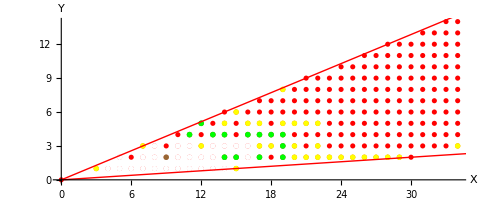

```mathematica
Plot2DSemigAll[goodExample[[1]],goodExample[[2]]]
```

### Huecos, huecos pseudo-Frobenius y especiales

```mathematica
Print["G(S) -> ",goodExample[[2]]]
gS = Length[goodExample[[2]]];
Print["g(S) -> ",Length[goodExample[[2]]]]

pseuFrobs = GetPseudoFrobenius[goodExample[[1]],goodExample[[2]]];
tS=Length[pseuFrobs];
Print["PF(S) -> ",pseuFrobs]
Print["t(S) -> ",tS]

espGaps=GetEspGaps[pseuFrobs,goodExample[[2]]];
Print["SG(S) -> ",espGaps]

espGaps == pseuFrobs
```

G(S) -> {{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{10,3},{11,1},{11,2},{11,3},{11,4},{12,1},{12,2},{12,5},{13,1},{13,2},{13,3},{13,4},{14,1},{14,2},{14,3},{14,4},{15,2},{15,3},{16,2},{16,3},{16,4},{17,2},{17,4},{18,4},{19,2},{19,3},{19,4}}

g(S) -> 40

PF(S) -> {{9,2},{11,4},{12,5},{13,4},{14,2},{14,4},{15,2},{16,4},{17,2},{17,4},{18,4},{19,2},{19,3},{19,4}}

t(S) -> 14

SG(S) -> {{11,4},{12,5},{13,4},{14,2},{14,4},{15,2},{16,4},{17,2},{17,4},{18,4},{19,2},{19,3},{19,4}}

False

### Vector Frobenius y N(S) en distintos órdenes

```mathematica
Print["Empleando orden Lexicográfico:"]
Print["v. Frob -> ",FrobeniusLexi[goodExample[[2]]]]
nLexi = NFrobeniusLexi[goodExample[[1]],goodExample[[2]]]

Print["Empleando orden Lexicográfico graduado:"]
Print["v. Frob -> ",FrobeniusDLexi[goodExample[[2]]]]
nDLexi = NFrobeniusDLexi[goodExample[[1]],goodExample[[2]]]

Print["Empleando orden Lexicográfico graduado inverso:"]
Print["v. Frob -> ",FrobeniusDRLexi[goodExample[[2]]]]
nDRLexi = NFrobeniusDRLexi[goodExample[[1]],goodExample[[2]]]

nLexi == nDLexi
nDLexi == nDRLexi
nLexi == nDRLexi
```

Empleando orden Lexicográfico:

v. Frob -> {19,4}

{{3,1},{6,2},{7,3},{9,3},{10,4},{12,3},{12,4},{13,5},{14,5},{14,6},{15,1},{15,4},{15,5},{15,6},{16,5},{16,6},{17,3},{17,5},{17,6},{17,7},{18,2},{18,3},{18,5},{18,6},{18,7}}

Empleando orden Lexicográfico graduado:

v. Frob -> {19,4}

{{3,1},{6,2},{7,3},{9,3},{10,4},{12,3},{12,4},{13,5},{14,5},{14,6},{15,1},{15,4},{15,5},{15,6},{16,5},{16,6},{17,3},{17,5},{17,6},{18,2},{18,3},{18,5},{20,2}}

Empleando orden Lexicográfico graduado inverso:

v. Frob -> {19,4}

{{3,1},{6,2},{7,3},{9,3},{10,4},{12,3},{12,4},{13,5},{14,5},{14,6},{15,1},{15,4},{15,5},{15,6},{16,5},{16,6},{17,3},{17,5},{17,6},{18,2},{18,3},{18,5},{20,2}}

False

True

False

### Desigualdad g(S) ≤ t(S)·n(S)

```mathematica
gS <= tS * Length[nLexi]
gS <= tS * Length[nDLexi]
gS <= tS * Length[nDRLexi]
```

True

True

True

Capítulo 2

## Ejemplo 2.1 en N.b2

### Semigrupo

```mathematica
goodExample={{{3,1},{7,3},{12,3},{14,5},{15,1},{15,6},{16,5},{17,3},{17,5},{18,3},{19,5},{19,8},{20,2},{20,3},{20,5},{21,2},{21,5},{22,2},{22,3},{23,2},{24,2},{25,2},{26,2},{27,2},{28,2},{29,2},{34,3},{22,5}},
{{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{10,3},{11,1},{11,2},{11,3},{11,4},{12,1},{12,2},{12,5},{13,1},{13,2},{13,3},{13,4},{14,1},{14,2},{14,3},{14,4},{15,2},{15,3},{16,2},{16,3},{16,4},{17,2},{17,4},{18,4},{19,2},{19,3},{19,4}}};
```

```mathematica
Plot2DSemigAll[goodExample[[1]],goodExample[[2]]]
```

Vectores de los rayos extremales= {{15,1},{7,3}}

-Graphics-

### Huecos, huecos pseudo-Frobenius y especiales

```mathematica
Print["G(S) -> ",goodExample[[2]]]
gS = Length[goodExample[[2]]];
Print["g(S) -> ",Length[goodExample[[2]]]]

pseuFrobs = GetPseudoFrobenius[goodExample[[1]],goodExample[[2]]];
tS=Length[pseuFrobs];
Print["PF(S) -> ",pseuFrobs]
Print["t(S) -> ",tS]

espGaps=GetEspGaps[pseuFrobs,goodExample[[2]]];
Print["SG(S) -> ",espGaps]

espGaps == pseuFrobs
```

G(S) -> {{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{10,3},{11,1},{11,2},{11,3},{11,4},{12,1},{12,2},{12,5},{13,1},{13,2},{13,3},{13,4},{14,1},{14,2},{14,3},{14,4},{15,2},{15,3},{16,2},{16,3},{16,4},{17,2},{17,4},{18,4},{19,2},{19,3},{19,4}}

g(S) -> 40

PF(S) -> {{9,2},{11,4},{12,5},{13,4},{14,2},{14,4},{15,2},{16,4},{17,2},{17,4},{18,4},{19,2},{19,3},{19,4}}

t(S) -> 14

SG(S) -> {{11,4},{12,5},{13,4},{14,2},{14,4},{15,2},{16,4},{17,2},{17,4},{18,4},{19,2},{19,3},{19,4}}

False

### Vector Frobenius y N(S) en distintos órdenes

```mathematica
Print["Empleando orden Lexicográfico:"]
Print["v. Frob -> ",FrobeniusLexi[goodExample[[2]]]]
nLexi = NFrobeniusLexi[goodExample[[1]],goodExample[[2]]]

Print["Empleando orden Lexicográfico graduado:"]
Print["v. Frob -> ",FrobeniusDLexi[goodExample[[2]]]]
nDLexi = NFrobeniusDLexi[goodExample[[1]],goodExample[[2]]]

Print["Empleando orden Lexicográfico graduado inverso:"]
Print["v. Frob -> ",FrobeniusDRLexi[goodExample[[2]]]]
nDRLexi = NFrobeniusDRLexi[goodExample[[1]],goodExample[[2]]]

nLexi == nDLexi
nDLexi == nDRLexi
nLexi == nDRLexi
```

Empleando orden Lexicográfico:

v. Frob -> {19,4}

{{3,1},{6,2},{7,3},{9,3},{10,4},{12,3},{12,4},{13,5},{14,5},{14,6},{15,1},{15,4},{15,5},{15,6},{16,5},{16,6},{17,3},{17,5},{17,6},{17,7},{18,2},{18,3},{18,5},{18,6},{18,7}}

Empleando orden Lexicográfico graduado:

v. Frob -> {19,4}

{{3,1},{6,2},{7,3},{9,3},{10,4},{12,3},{12,4},{13,5},{14,5},{14,6},{15,1},{15,4},{15,5},{15,6},{16,5},{16,6},{17,3},{17,5},{17,6},{18,2},{18,3},{18,5},{20,2}}

Empleando orden Lexicográfico graduado inverso:

v. Frob -> {19,4}

{{3,1},{6,2},{7,3},{9,3},{10,4},{12,3},{12,4},{13,5},{14,5},{14,6},{15,1},{15,4},{15,5},{15,6},{16,5},{16,6},{17,3},{17,5},{17,6},{18,2},{18,3},{18,5},{20,2}}

False

True

False

### Desigualdad g(S) ≤ t(S)·n(S)

```mathematica
gS <= tS * Length[nLexi]
gS <= tS * Length[nDLexi]
gS <= tS * Length[nDRLexi]
```

True

True

True

## Probando Cosas

## Generando

### Cono

Cono generado por los elementos de A

Vectores de los rayos extremales= {{15,1},{7,3}}

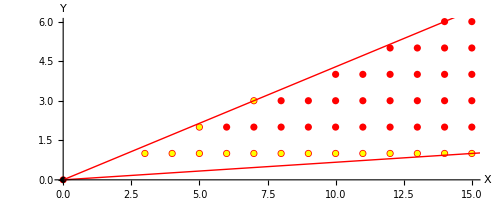

```mathematica
fileDirectory=NotebookDirectory[];
A={{10,9},{7,1}};
{hilb,Eq}=ConeGenSupHyp[A,fileDirectory];
Plot2DSemig[hilb,{{0,0}}]
```

### Semigrupos

Al cono anterior, empleando las formulas obtenidas, generamos un semigrupo quitando huecos de manera aleatoria.

```mathematica
fileDirectory=NotebookDirectory[];
A={{10,9},{7,1}};
{hilb,Eq}=ConeGenSupHyp[A,fileDirectory];

nHuecos=10
quitaHuecos=SemigroupGenusToDFromGenEqEnRama[hilb,Eq,fileDirectory,nHuecos,A,0]
Plot2DSemig[quitaHuecos[[1]],quitaHuecos[[2]]]
```

### Semigrupos con radios

```mathematica
fileDirectory=NotebookDirectory[];
A={{30,2},{7,3}};

{hilb,Eq}=ConeGenSupHyp[A,fileDirectory];

nHuecos=40;
{r1,r2}={(4)^2,(20)^2};

KK=SemigroupGenusToDFromGenEqEnRamaSinQuitarDeEjesYEnCirculo[hilb,Eq,fileDirectory,nHuecos,A,0,r1,r2]
If[KK≠{},Plot2DSemigAll[KK[[1]],KK[[2]]]]
```

## Generando a la fuerza con Pseudos no Especiales

```mathematica
(*GENERANDO A LA FUERZA*)
(**Dirección archivo**)
fileDirectory=NotebookDirectory[];
(**Aristas del cono**)
A={{30,2},{7,3}};

(**Obteniendo ecuaciones del cono**)
{hilb,Eq}=ConeGenSupHyp[A,fileDirectory];

(**N.ba de huecos deseados**)
nHuecos=10;
{r1,r2}={(4)^2,(25)^2};

(**N.ba de huecos deseados**)
nDePseudosNoEsp=2;

contador=0;
posibleSN={};
nNoPs =1;

While[(posibleSN=={})∨(nNoPs<nDePseudosNoEsp),
Print[contador];
posibleSN=SemigroupGenusToDFromGenEqEnRamaSinQuitarDeEjesYEnCirculo[hilb,Eq,fileDirectory,nHuecos,A,0,r1,r2];
psFrobPosSN =GetPseudoFrobenius[posibleSN[[1]],posibleSN[[2]] ];
espGapPosSN=GetEspGaps[psFrobPosSN,posibleSN[[2]] ];
nNoPs=Length[psFrobPosSN]-Length[espGapPosSN];
contador++;
];

posibleSN;
prueba={posibleSN,Eq}
contador
Plot2DSemigAll[posibleSN[[1]],posibleSN[[2]]];
```

```mathematica
(*PRUEBA DE LO OBTENIDO*)
prueba={posibleSN,Eq};

Print["Huecos -> ",Length[prueba[[1,2]]]]
p = GetPseudoFrobenius[prueba[[1,1]],prueba[[1,2]]];
Print["Ps -> ",Length[ GetPseudoFrobenius[prueba[[1,1]],prueba[[1,2]]]]];
Print["Sg -> ",Length[ GetEspGaps[p,prueba[[1,2]]]]]

Print["Irreducibles Alg1"]
Timing [testirr = GetIrreducibles[prueba[[1,1]],prueba[[1,2]],prueba[[2]],False]]
Length[testirr]

Print["Minimos Irreducibles Alg2"]
Timing [testminirr = GetMinimalsIrreducibles[prueba[[1,1]],prueba[[1,2]],prueba[[2]],False,False]]
Length[testminirr]
Length[testirr]
```

```mathematica
(*COMPRANDO SI INTERSECCION DA EL SEMIGRUPO*)
testminirr[[1;;,1]]

aux=testminirr[[1,1]]

For[i=2,i≤Length[testminirr]-2,i++,
	aux=Intersection[aux,testminirr[[i,1]]]
]
aux
```

## Posibles Ejemplos Buenos

### Ejemplo Inicial

#### Semigrupo

```mathematica
goodExample={{{3,1},{4,1},{7,3},{21,5},{22,5},{22,9},{23,4},{23,5},{24,5},{25,3},{25,4},{26,3},{26,4},{26,11},{31,2},{37,5},{39,6},{48,6},{49,5},{49,6},{50,4},{50,5},{51,4},{51,5},{52,4},{52,5},{53,4},{54,4},{55,4},{56,4},{57,4},{58,4},{59,4},{60,4},{61,4},{67,5},{68,5},{69,5},{70,5},{71,5},{72,5},{73,5},{74,5},{75,5},{76,5},{77,5},{25,5}},

{{5,1},{5,2},{6,1},{7,1},{8,1},{8,3},{9,1},{9,2},{10,1},{10,2},{11,1},{11,2},{12,1},{12,2},{12,5},{13,1},{13,2},{13,3},{14,1},{14,2},{14,3},{15,1},{15,2},{15,3},{15,6},{16,2},{16,3},{17,2},{17,3},{17,4},{18,2},{18,3},{18,4},{19,2},{19,3},{19,4},{19,8},{20,2},{20,3},{20,4},{21,2},{21,3},{21,4},{22,2},{22,3},{22,4},{23,2},{23,3},{24,2},{24,3},{24,4},{25,2},{26,2},{27,2},{27,3},{27,4},{28,2},{28,3},{29,2},{29,3},{30,2},{30,3},{31,3},{31,4},{32,3},{32,4},{33,3},{33,4},{34,4},{35,4},{35,5},{36,3},{36,4},{36,5},{37,3},{38,3},{39,3},{39,5},{40,3},{40,4},{41,3},{41,4},{42,3},{42,4},{43,3},{43,4},{44,3},{44,4},{44,5},{45,3},{45,4},{45,5},{46,3},{46,4},{46,5},{47,4},{47,5},{48,4},{48,5},{49,4}}};
```

```mathematica
Plot2DSemigAll[goodExample[[1]],goodExample[[2]]]
```

#### Gaps, PseudoFrobs y Especial Gaps

```mathematica
goodExample[[2]];
pseuFrobs = GetPseudoFrobenius[goodExample[[1]],goodExample[[2]]]
espGaps=GetEspGaps[pseuFrobs,goodExample[[2]]]
espGaps == pseuFrobs
```

{{15,6},{17,4},{18,4},{19,4},{19,8},{20,4},{21,4},{22,3},{22,4},{24,4},{27,4},{34,4},{35,5},{36,5},{39,5},{44,5},{45,5},{46,4},{46,5},{47,4},{47,5},{48,4},{48,5},{49,4}}

{{15,6},{17,4},{18,4},{19,4},{19,8},{20,4},{21,4},{22,3},{22,4},{24,4},{27,4},{34,4},{35,5},{36,5},{39,5},{44,5},{45,5},{46,4},{46,5},{47,4},{47,5},{48,4},{48,5},{49,4}}

True

### Ejemplo con un solo Pseudo no especial

#### Semigrupo

```mathematica
goodExample={{{3,1},{7,3},{12,3},{14,5},{15,1},{15,6},{16,5},{17,3},{17,5},{18,3},{19,5},{19,8},{20,2},{20,3},{20,5},{21,2},{21,5},{22,2},{22,3},{23,2},{24,2},{25,2},{26,2},{27,2},{28,2},{29,2},{34,3},{22,5}},
{{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{10,3},{11,1},{11,2},{11,3},{11,4},{12,1},{12,2},{12,5},{13,1},{13,2},{13,3},{13,4},{14,1},{14,2},{14,3},{14,4},{15,2},{15,3},{16,2},{16,3},{16,4},{17,2},{17,4},{18,4},{19,2},{19,3},{19,4}}};
```

Vectores de los rayos extremales= {{15,1},{7,3}}

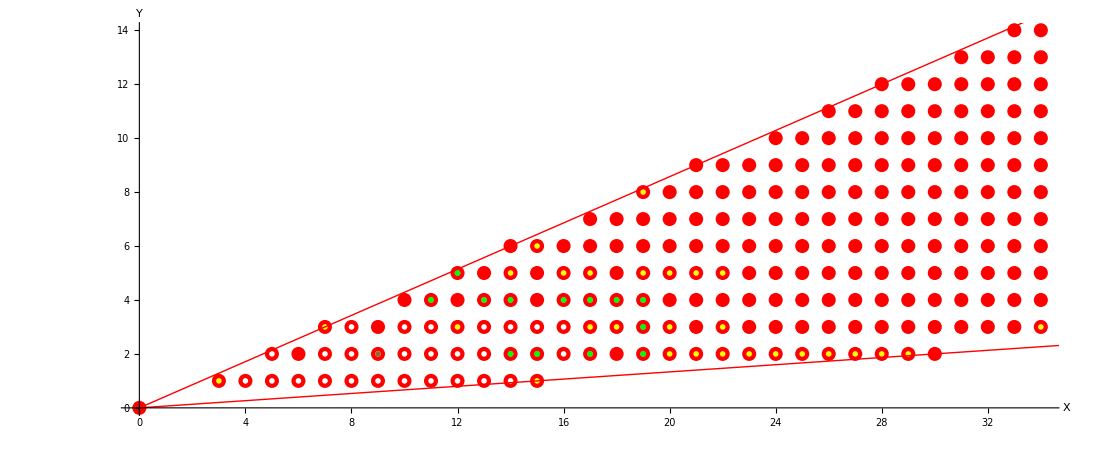

```mathematica
Plot2DSemigAll[goodExample[[1]],goodExample[[2]]]
```

#### Gaps, PseudoFrobs y Especial Gaps

```mathematica
goodExample[[2]];
pseuFrobs = GetPseudoFrobenius[goodExample[[1]],goodExample[[2]]]
espGaps=GetEspGaps[pseuFrobs,goodExample[[2]]]
espGaps == pseuFrobs
```

#### Alg 1 y 2

```mathematica
goodExample3= {{{3,1},{7,3},{12,3},{14,5},{15,1},{15,6},{16,5},{17,3},{17,5},{18,3},{19,5},{19,8},{20,2},{20,3},{20,5},{21,2},{21,5},{22,2},{22,3},{23,2},{24,2},{25,2},{26,2},{27,2},{28,2},{29,2},{34,3},{22,5}},
{{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{10,3},{11,1},{11,2},{11,3},{11,4},{12,1},{12,2},{12,5},{13,1},{13,2},{13,3},{13,4},{14,1},{14,2},{14,3},{14,4},{15,2},{15,3},{16,2},{16,3},{16,4},{17,2},{17,4},{18,4},{19,2},{19,3},{19,4}}};
```

```mathematica
Print["Huecos -> ",Length[goodExample3⟦2⟧]]
p=GetPseudoFrobenius[goodExample3⟦1⟧,goodExample3⟦2⟧];
Print["Ps -> ",Length[GetPseudoFrobenius[goodExample3⟦1⟧,goodExample3⟦2⟧]]];
Print["Sg -> ",Length[GetEspGaps[p,goodExample3⟦2⟧]]]

(* Vectores de los rayos extremales para sacar ecuaciones del*)
T1=ConvexHullMesh[Join @@ {{{0,0}},goodExample3[[1]]}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0.,0.}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0.,0.}&];

(*Ecuaciones del cono para comprobar si punto está en el cono*)
Eq = ConeGenSupHyp[vectorsinrays,fileDirectory][[2]];

Timing[testminirr=GetMinimalsIrreducibles[goodExample3⟦1⟧,goodExample3⟦2⟧,Eq,False,False]]
Length[testminirr]
Length[testirr]
```

Huecos -> 40

Ps -> 14

Sg -> 13

Out getsinfo -> {{11,18,21,25,27,29,30,34,35,36,37,38,39,40},{18,21,25,27,29,30,34,35,36,37,38,39,40},13}

N.ba de #C 13

N.ba de #C 78

N.ba de #C 289

N.ba de #C 745

N.ba de #C 1423

N.ba de #C 2085

$Aborted

13

5

### Ejemplo con dos Pseudo no especial

#### Semigrupo

Vectores de los rayos extremales= {{15.,1.},{7.,3.}}

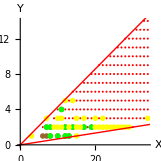

```mathematica
goodExample2= {{{3,1},{7,3},{9,2},{10,2},{10,3},{11,2},{11,3},{12,5},{13,2},{14,5},{15,1},{15,2},{15,3},{16,2},{17,3},{20,2},{21,2},{22,2},{22,3},{23,2},{24,2},{25,2},{26,2},{27,2},{28,2},{29,2},{34,3},{20,3}},{{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{10,1},{11,1},{11,4},{12,1},{12,2},{13,1},{14,1},{14,2},{17,2},{19,2}}};

Plot2DSemigAll[goodExample2[[1]],goodExample2[[2]]];
```

#### Gaps, PseudoFrobs y Especial Gaps

```mathematica
goodExample2[[2]];
pseuFrobs2 = GetPseudoFrobenius[goodExample2[[1]],goodExample2[[2]]]
espGaps2 =GetEspGaps[pseuFrobs2,goodExample2[[2]]]
numNoPs=Length[psFrobPosSN]-Length[espGapPosSN]
```

#### Alg 1 y 2

```mathematica
goodExample3= {{{3,1},{7,3},{9,2},{10,2},{10,3},{11,2},{11,3},{12,5},{13,2},{14,5},{15,1},{15,2},{15,3},{16,2},{17,3},{20,2},{21,2},{22,2},{22,3},{23,2},{24,2},{25,2},{26,2},{27,2},{28,2},{29,2},{34,3},{20,3}},{{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{10,1},{11,1},{11,4},{12,1},{12,2},{13,1},{14,1},{14,2},{17,2},{19,2}}};
```

```mathematica
Print["Huecos -> ",Length[goodExample3⟦2⟧]]
p=GetPseudoFrobenius[goodExample3⟦1⟧,goodExample3⟦2⟧];
Print["Ps -> ",Length[GetPseudoFrobenius[goodExample3⟦1⟧,goodExample3⟦2⟧]]];
Print["Sg -> ",Length[GetEspGaps[p,goodExample3⟦2⟧]]]

(* Vectores de los rayos extremales para sacar ecuaciones del*)
T1=ConvexHullMesh[Join @@ {{{0,0}},goodExample3[[1]]}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0.,0.}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0.,0.}&];

(*Ecuaciones del cono para comprobar si punto está en el cono*)
Eq = ConeGenSupHyp[vectorsinrays,fileDirectory][[2]];

Timing[testminirr=GetMinimalsIrreducibles[goodExample3⟦1⟧,goodExample3⟦2⟧,Eq,False,False]]
Length[testminirr]
Length[testirr]
```

Huecos -> 20

Ps -> 13

Sg -> 11

Out getsinfo -> {{4,5,6,7,8,11,13,14,15,16,18,19,20},{6,7,8,11,13,14,15,16,18,19,20},11}

N.ba de #C 11

N.ba de #C 55

N.ba de #C 170

N.ba de #C 366

N.ba de #C 578

$Aborted

3

5

### Ejemplo con tres Pseudo no especial

#### Semigrupo

Vectores de los rayos extremales= {{15.,1.},{21.,9.}}

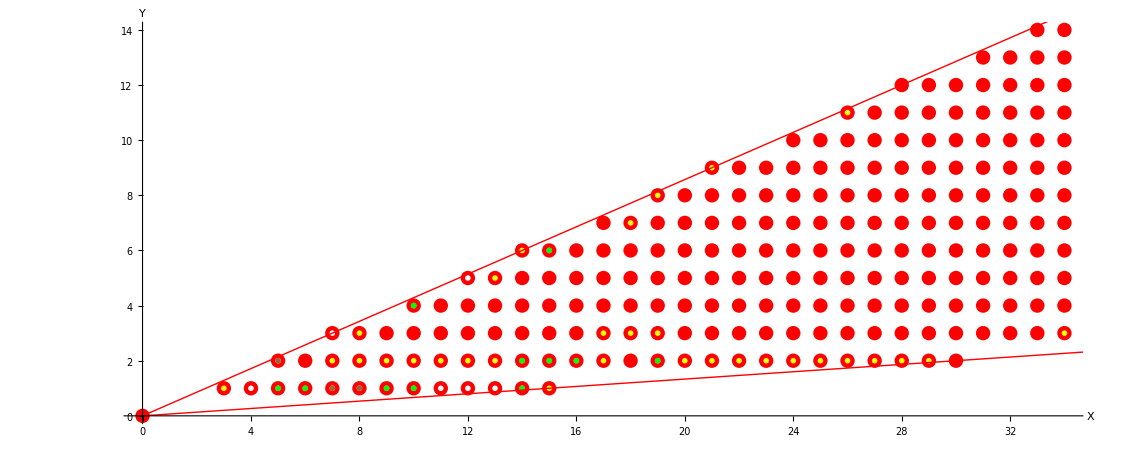

```mathematica
goodExample32={{{7,3},{9,3},{10,1},{10,2},{12,2},{13,3},{14,4},{14,5},{15,1},{15,2},{15,3},{15,4},{16,5},{17,6},{17,7},{18,2},{19,7},{19,8},{21,2},{21,3},{21,4},{22,2},{22,9},{23,2},{26,2},{27,2},{27,11},{28,2},{29,2},{8,2},{11,4},{12,3},{13,4},{14,2},{14,3},{16,3},{18,5},{19,2},{19,3},{26,3}},{{3,1},{4,1},{5,1},{5,2},{6,1},{6,2},{7,1},{7,2},{8,1},{8,3},{9,1},{9,2},{10,3},{10,4},{11,1},{11,2},{11,3},{12,1},{12,4},{12,5},{13,1},{13,2},{13,5},{14,1},{15,6},{16,2},{17,2},{17,3},{20,8},{24,2}}};
goodExample3= {(*Geners*){{3,1},{7,2},{8,2},{8,3},{9,2},{10,2},{11,2},{12,2},{13,2},{13,5},{14,6},{15,1},{17,2},{18,3},{18,7},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2
},{28,2},{29,2},{34,3},{17,3}},
(*Huecos*){{4,1},{5,1},{5,2},{6,1},{7,1},{7,3},{8,1},{9,1},{10,1},{10,4},{11,1},{12,1},{12,5},{13,1},{14,1},{14,2},{15,2},{15,6},{16,2},{19,2}}};

Plot2DSemigAll[goodExample3[[1]],goodExample3[[2]]];
```

#### Gaps, PseudoFrobs y Especial Gaps

{{5,1},{5,2},{6,1},{7,1},{8,1},{9,1},{10,1},{10,4},{14,1},{14,2},{15,2},{15,6},{16,2},{19,2}}

{{5,1},{6,1},{9,1},{10,1},{10,4},{14,1},{14,2},{15,2},{15,6},{16,2},{19,2}}

{{5,1},{6,1},{9,1},{10,1},{10,4},{14,1},{14,2},{15,2},{15,6},{16,2},{19,2}}

True

{{4,1},{5,1},{6,1},{7,3},{9,1},{10,1},{10,4},{11,1},{12,1},{12,5},{13,1},{14,1},{14,2},{15,2},{15,6},{16,2},{19,2}}

11

14

PseudoFrobs = EspecialGaps --> False
Diferencia : 3

PseudoFrobs = FundGaps --> False

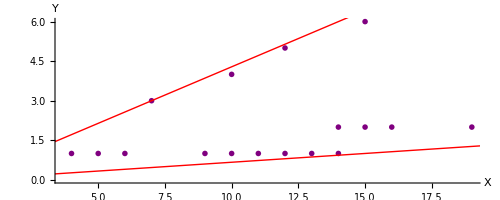

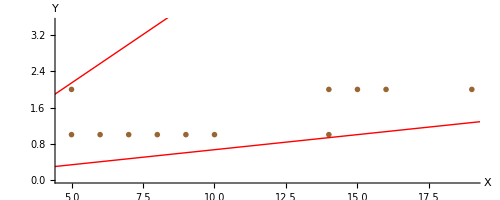

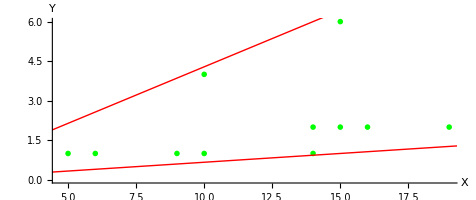

```mathematica
(*Calculando conjuntos*)
pseuFrobs3 = GetPseudoFrobenius[goodExample3[[1]],goodExample3[[2]]]
espGaps3 =GetEspGaps[pseuFrobs3,goodExample3[[2]]]
espGaps32 = GetEspGapsGen[goodExample3[[1]],goodExample3[[2]]]
espGaps3==espGaps32
fundGaps3 = GetFundGaps[goodExample3[[2]]]
Print[Length[espGaps3]]
Print[Length[pseuFrobs3]]


(* Algunas comparaciones*)
numNoPs=Length[pseuFrobs3]-Length[espGaps3];
Print["PseudoFrobs = EspecialGaps --> ",pseuFrobs3==espGaps3,
"\nDiferencia : ",numNoPs]
Print["PseudoFrobs = FundGaps --> ",pseuFrobs3==fundGaps3]

(* Vectores de los rayos extremales para sacar ecuaciones del cono.*)
T1=ConvexHullMesh[Join @@ {{{0,0}},goodExample3[[1]]}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0.,0.}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0.,0.}&];
vectorsinrays=ParallelTable[{{0,0},20*vectorsinrays[[i]]},{i,Length[vectorsinrays]}];

(*Representación gráfica fundGaps4*)
Print[
Show[
{
ListPlot[fundGaps3,PlotStyle->Purple,PlotMarkers->"OpenMarkers"],
Graphics[{Red,Thick,Line[vectorsinrays]}]
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
]
];

(*Representación gráfica pseuFrobs4*)
Print[
Show[
{
ListPlot[pseuFrobs3,PlotStyle->Brown,PlotMarkers->"OpenMarkers"],
Graphics[{Red,Thick,Line[vectorsinrays]}]
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
]
];

(*Representación gráfica espGaps4*)
Print[
Show[
{
ListPlot[espGaps3,PlotStyle->Green,PlotMarkers->"OpenMarkers"],
Graphics[{Red,Thick,Line[vectorsinrays]}]
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
]
];
```

#### Alg 1 y 2

```mathematica
Print["Huecos -> ",Length[goodExample3⟦2⟧]]
p=GetPseudoFrobenius[goodExample3⟦1⟧,goodExample3⟦2⟧];
Print["Ps -> ",Length[GetPseudoFrobenius[goodExample3⟦1⟧,goodExample3⟦2⟧]]];
Print["Sg -> ",Length[GetEspGaps[p,goodExample3⟦2⟧]]]

(* Vectores de los rayos extremales para sacar ecuaciones del*)
T1=ConvexHullMesh[Join @@ {{{0,0}},goodExample3[[1]]}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0.,0.}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0.,0.}&];

(*Ecuaciones del cono para comprobar si punto está en el cono*)
Eq = ConeGenSupHyp[vectorsinrays,fileDirectory][[2]];

Timing[testminirr=GetMinimalsIrreducibles[goodExample3⟦1⟧,goodExample3⟦2⟧,Eq,False,False]]
Length[testminirr]
Length[testirr]
```

Huecos -> 20

Ps -> 2

Sg -> 14

Out getsinfo -> {{2,3,4,5,7,8,9,10,15,16,17,18,19,20},{2,4,8,9,10,15,16,17,18,19,20},11}

N.ba de #C 11

N.ba de #C 49

N.ba de #C 124

N.ba de #C 210

N.ba de #C 254

N.ba de #C 223

N.ba de #C 140

N.ba de #C 45

N.ba de #C 31

N.ba de #C 31

N.ba de #C 12

N.ba irreducibles 1 -> 72

{{{{3,1},{5,1},{6,1},{7,2},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,1},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{14,2}}},{{{3,1},{5,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{6,1},{7,1},{7,3},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{14,2}}},{{{3,1},{6,1},{7,2},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,1},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,2}}},{{{3,1},{7,2},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,1},{7,3},{8,1},{10,1},{11,1},{12,1},{12,5},{13,1},{19,2}}},{{{3,1},{7,2},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,1},{7,3},{8,1},{10,1},{11,1},{12,1},{12,5},{13,1},{16,2}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{19,2}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{15,6},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{16,2}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{15,6}}},{{{3,1},{5,1},{6,1},{7,2},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,1},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{15,2}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,2},{8,3},{9,2},{10,2},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{8,1},{9,1},{10,1},{10,4},{11,1},{12,1},{12,5},{13,1},{14,1}}},{{{3,1},{5,1},{6,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,1},{7,3},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{15,2}}},{{{3,1},{6,1},{7,1},{7,2},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{19,2}}},{{{3,1},{6,1},{7,1},{7,2},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{16,2}}},{{{3,1},{6,1},{7,1},{7,2},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{15,6}}},{{{3,1},{6,1},{7,2},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,1},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{6,1},{7,1},{7,2},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{15,2}}},{{{3,1},{6,1},{7,1},{7,2},{8,2},{8,3},{9,2},{10,2},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,3},{8,1},{9,1},{10,1},{10,4},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,1},{7,3},{10,1},{11,1},{12,1},{12,5},{13,1},{15,6}}},{{{3,1},{7,2},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,1},{7,3},{8,1},{10,1},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,1},{7,3},{10,1},{11,1},{12,1},{12,5},{13,1},{15,2}}},{{{3,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,1},{7,3},{10,1},{11,1},{12,1},{12,5},{13,1},{14,2}}},{{{3,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,1},{7,3},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1}}},{{{3,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,2},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,1},{7,3},{10,1},{10,4},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{7,1},{7,2},{8,2},{8,3},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{9,1},{11,1},{12,1},{12,5},{13,1},{19,2}}},{{{3,1},{7,1},{7,2},{8,2},{8,3},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{9,1},{11,1},{12,1},{12,5},{13,1},{16,2}}},{{{3,1},{7,1},{7,2},{8,2},{8,3},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{9,1},{11,1},{12,1},{12,5},{13,1},{15,2}}},{{{3,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,1},{7,3},{9,1},{11,1},{12,1},{12,5},{13,1},{15,2}}},{{{3,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,1},{7,3},{9,1},{11,1},{12,1},{12,5},{13,1},{14,2}}},{{{3,1},{7,1},{7,2},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{10,1},{11,1},{12,1},{12,5},{13,1},{19,2}}},{{{3,1},{7,1},{7,2},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{10,1},{11,1},{12,1},{12,5},{13,1},{15,6}}},{{{3,1},{7,1},{7,2},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{10,1},{11,1},{12,1},{12,5},{13,1},{15,2}}},{{{3,1},{5,1},{7,1},{7,2},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{6,1},{7,3},{8,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{19,2}}},{{{3,1},{5,1},{7,1},{7,2},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{6,1},{7,3},{8,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{15,6}}},{{{3,1},{5,1},{7,1},{7,2},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{6,1},{7,3},{8,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{15,2}}},{{{3,1},{7,1},{7,2},{8,2},{8,3},{9,1},{9,2},{10,2},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{10,1},{10,4},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{5,1},{7,1},{7,2},{8,2},{8,3},{9,1},{9,2},{10,2},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{6,1},{7,3},{8,1},{10,1},{10,4},{11,1},{12,1},{12,5},{13,1},{14,1}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1}}},{{{3,1},{5,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{6,1},{7,3},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{15,6}}},{{{3,1},{5,1},{6,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,1},{7,3},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,2},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{9,1},{10,1},{10,4},{11,1},{12,1},{12,5},{13,1},{14,1}}},{{{3,1},{6,1},{7,1},{7,2},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,3},{9,1},{11,1},{12,1},{12,5},{13,1},{15,6}}},{{{3,1},{7,1},{7,2},{8,2},{8,3},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{9,1},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,1},{7,3},{9,1},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,3},{9,1},{11,1},{12,1},{12,5},{13,1},{14,1}}},{{{3,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,1},{10,2},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,3},{9,1},{10,4},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{6,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,1},{7,3},{9,1},{11,1},{12,1},{12,5},{13,1},{15,2}}},{{{3,1},{5,1},{7,1},{7,2},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{6,1},{7,3},{8,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1}}},{{{3,1},{7,1},{7,2},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{10,1},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,3},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,3},{9,1},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,3},{9,1},{11,1},{12,1},{12,5},{13,1},{15,6}}},{{{3,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,1},{10,2},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,3},{9,1},{10,4},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,3},{10,1},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{6,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,1},{7,3},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,3},{9,1},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{6,1},{7,3},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,3},{11,1},{12,1},{12,5},{13,1},{15,6}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{9,1},{11,1},{12,1},{12,5},{13,1},{14,1}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{9,1},{11,1},{12,1},{12,5},{13,1},{15,6}}},{{{3,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,3},{10,4},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,1},{10,2},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{9,1},{10,4},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{11,1},{12,1},{12,5},{13,1},{14,1}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{10,1},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{5,1},{6,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,1},{7,3},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,1},{5,2},{7,3},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{9,1},{11,1},{12,1},{12,5},{13,1}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{10,4},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{11,1},{12,1},{12,5},{13,1},{15,6}}},{{{3,1},{5,1},{6,1},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{9,2},{10,1},{10,2},{11,2},{12,2},{13,2},{13,5},{14,1},{14,2},{14,6},{15,1},{15,2},{15,6},{16,2},{17,2},{17,3},{18,3},{18,7},{19,2},{19,3},{19,8},{20,2},{21,2},{21,9},{22,2},{23,2},{24,2},{25,2},{26,2},{26,11},{27,2},{28,2},{29,2},{34,3}},{{4,1},{5,2},{7,3},{10,4},{11,1},{12,1},{12,5},{13,1}}}}

$Aborted

3

5

### Ejemplo con cuatro Pseudo no especial

Usado en el bucle
nHuecos = 30;
A={{30,2},{7,3}};
{r1, r2} = {(4)^2, (25)^2};

#### Semigrupo

```mathematica
goodExample4={{{7,3},{9,2},{9,3},{10,2},{10,3},{11,4},{12,2},{12,3},{12,5},{13,2},{13,4},{13,5},{14,3},{14,4},{14,5},{15,1},{15,4},{15,6},{16,2},{16,3},{17,2},{17,3},{18,2},{19,2},{19,3},{19,7},{20,3},{21,2},{21,3},{22,3},{23,2},{25,2},{26,2},{26,3},{27,2},{28,2},{29,2},{29,3},{30,3},{35,3},{37,3},{39,3},{15,5},{16,4},{17,4},{23,3}},{{3,1},{4,1},{5,1},{5,2},{6,1},{6,2},{7,1},{7,2},{8,1},{8,2},{8,3},{9,1},{10,1},{10,4},{11,1},{11,2},{11,3},{12,1},{12,4},{13,1},{13,3},{14,1},{14,2},{15,2},{15,3},{17,7},{18,3},{20,2},{22,2},{24,2}}};

Plot2DSemigAll[goodExample4[[1]],goodExample4[[2]]];
```

#### PseudoFrobs, Especial Gaps y Fund Gaps

```mathematica
(*Calculando conjuntos*)
pseuFrobs4 = GetPseudoFrobenius[goodExample4[[1]],goodExample4[[2]]]
espGaps4 =GetEspGaps[pseuFrobs4,goodExample4[[2]]]
espGaps42 = GetEspGapsGen[goodExample4[[1]],goodExample4[[2]]]
espGaps4==espGaps42
fundGaps4 = GetFundGaps[goodExample4[[2]]]
Print[Length[espGaps4]]
Print[Length[pseuFrobs4]]


(* Algunas comparaciones*)
numNoPs=Length[pseuFrobs4]-Length[espGaps4];
Print["PseudoFrobs = EspecialGaps --> ",pseuFrobs4==espGaps4,
"\nDiferencia : ",numNoPs]
Print["PseudoFrobs = FundGaps --> ",pseuFrobs4==fundGaps4]

(* Vectores de los rayos extremales para sacar ecuaciones del cono.*)
T1=ConvexHullMesh[Join @@ {{{0,0}},goodExample4[[1]]}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0.,0.}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0.,0.}&];
vectorsinrays=ParallelTable[{{0,0},20*vectorsinrays[[i]]},{i,Length[vectorsinrays]}];

(*Representación gráfica fundGaps4*)
Print[
Show[
{
ListPlot[fundGaps4,PlotStyle->Purple,PlotMarkers->"OpenMarkers"],
Graphics[{Red,Thick,Line[vectorsinrays]}]
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
]
];

(*Representación gráfica pseuFrobs4*)
Print[
Show[
{
ListPlot[pseuFrobs4,PlotStyle->Brown,PlotMarkers->"OpenMarkers"],
Graphics[{Red,Thick,Line[vectorsinrays]}]
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
]
];

(*Representación gráfica espGaps4*)
Print[
Show[
{
ListPlot[espGaps4,PlotStyle->Green,PlotMarkers->"OpenMarkers"],
Graphics[{Red,Thick,Line[vectorsinrays]}]
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
]
];
```

#### Apery

```mathematica
(*Punto y directorio del archivo*)
fileDirectory=NotebookDirectory[];
pto= goodExample4[[1]][[1]];

(* Vectores de los rayos extremales para sacar ecuaciones del*)
T1=ConvexHullMesh[Join @@ {{{0,0}},goodExample4[[1]]}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0.,0.}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0.,0.}&];

(*Ecuaciones del cono para comprobar si punto está en el cono*)
Eq=ConeGenSupHyp[vectorsinrays,fileDirectory][[2]];

(*Calculo del apery con las dos funciones*)
Print["Apery del semigrupo con punto: ",pto];
aperyNoEq=GetApery[pto,goodExample4[[1]],goodExample4[[2]],fileDirectory]
aperyEq =GetAperyEq[pto,goodExample4[[2]],Eq];

aperyEq==aperyNoEq

(*Representación gráfica Apery*)
vectorsinrays=ParallelTable[{{0,0},20*vectorsinrays[[i]]},{i,Length[vectorsinrays]}]

Print[
Show[
{
ListPlot[aperyEq,PlotStyle->Yellow],
Graphics[{Red,Thick,Line[vectorsinrays]}]
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
]
];
```

#### I(n) set

```mathematica
(*Punto y directorio del archivo*)
fileDirectory=NotebookDirectory[];
pto={30,8};

(* Vectores de los rayos extremales para sacar ecuaciones del cono.
T1=ConvexHullMesh[Join @@ {{{0,0}},goodExample4[[1]]}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0.,0.}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0.,0.}&];

Eq=ConeGenSupHyp[vectorsinrays,fileDirectory][[2]];
*)

(*Calculo de I(n) con las dos funciones*)
Print["Conjunto I(n) con n=",pto];

iset=GetIsetEq[pto,goodExample4[[1]],goodExample4[[2]],Eq]
isetn=GetIsetNoEq[pto,goodExample4[[1]],goodExample4[[2]],fileDirectory];

(*Comprobación ambas funciones*)
iset == isetn

(*Representación gráfica*)
Print[
Show[
{
ListPlot[iset,PlotStyle->Orange],
Graphics[{Red,Thick,Line[vectorsinrays]}]
},
AxesOrigin->{0,0},AspectRatio->Automatic,Show->True,AxesLabel->{X,Y}
]
];
```

#### Irreducibles no depurado

```mathematica
(*Punto y directorio del archivo*)
fileDirectory=NotebookDirectory[];

(* Vectores de los rayos extremales para sacar ecuaciones del*)
T1=ConvexHullMesh[Join @@ {{{0,0}},goodExample4[[1]]}];
LineasT1=MeshPrimitives[T1,1];
T1L=Select[Level[LineasT1,{2}],MemberQ[#,{0.,0.}]&];
vectorsinrays=Select[Flatten[T1L,1],# !={0.,0.}&];

(*Ecuaciones del cono para comprobar si punto está en el cono*)
Eq = ConeGenSupHyp[vectorsinrays,fileDirectory][[2]];
```

```mathematica
setIrreducibles4={{{11,16,17,19,21,6,23,24,25,26,28,29,13,15,30},{27}},{{8,10,11,16,17,20,21,22,23,24,25,26,27,28,29,30},{19}},{{8,11,16,17,19,20,6,21,23,24,25,26,28,29,13,30},{27}},{{8,11,16,17,20,21,23,24,25,26,27,28,29,13,10,30},{19}},{{10,11,16,17,19,29,6,15,21,22,23,24,25,26,27,28},{30}},{{11,16,17,21,23,24,25,26,27,28,29,13,10,15,8,30},{19}},{{8,10,11,16,17,19,20,6,21,22,23,24,25,26,27,28,29},{30}},{{8,10,11,16,17,19,20,6,21,22,23,24,25,26,27,28,30},{29}},{{8,10,11,16,17,19,20,6,21,22,23,24,25,26,27,29,30},{28}},{{8,10,11,16,17,19,20,6,21,22,23,24,25,26,28,29,30},{27}},{{8,10,11,16,17,19,20,6,21,22,23,24,25,27,28,29,30},{26}},{{8,10,11,16,17,19,20,6,21,22,23,24,26,27,28,29,30},{25}},{{8,10,11,16,17,19,20,6,21,22,23,25,26,27,28,29,30},{24}},{{8,10,11,16,17,19,20,6,21,22,24,25,26,27,28,29,30},{23}},{{8,10,11,16,17,19,20,6,21,23,24,25,26,27,28,29,30},{22}},{{8,10,11,16,17,19,20,6,22,23,24,25,26,27,28,29,30},{21}},{{8,10,11,16,17,19,20,21,22,23,24,25,26,27,28,29,30},{6}},{{8,10,11,16,17,19,21,6,22,23,24,25,26,27,28,29,30},{20}},{{8,10,11,16,19,20,6,21,22,23,24,25,26,27,28,29,30},{17}},{{8,10,11,17,19,20,6,21,22,23,24,25,26,27,28,29,30},{16}},{{8,10,16,17,19,20,6,21,22,23,24,25,26,27,28,29,30},{11}},{{8,11,16,17,19,20,6,21,22,23,24,25,26,27,28,29,30},{10}},{{8,11,16,17,19,20,6,21,23,24,25,26,27,28,29,13,10},{30}},{{8,11,16,17,19,20,6,21,23,24,25,26,27,28,29,13,30},{10}},{{8,11,16,17,19,20,6,21,23,24,25,26,28,30,13,22,29},{27}},{{8,11,16,17,19,20,6,21,23,24,25,27,28,29,13,10,30},{26}},{{8,11,16,17,19,20,6,21,23,24,26,27,28,29,13,10,30},{25}},{{8,11,16,17,19,20,6,21,23,25,26,27,28,29,13,10,30},{24}},{{8,11,16,17,19,20,6,21,24,25,26,27,28,29,13,10,30},{23}},{{8,11,16,17,19,20,6,23,24,25,26,27,28,29,13,10,30},{21}},{{8,11,16,17,19,20,21,23,24,25,26,27,28,29,13,10,30},{6}},{{8,11,16,17,19,21,6,23,24,25,26,27,28,29,13,10,30},{20}},{{8,11,16,17,20,21,23,24,25,26,27,28,30,13,10,22,29},{19}},{{8,11,16,19,20,6,21,23,24,25,26,27,28,29,13,10,30},{17}},{{8,11,17,19,20,6,21,23,24,25,26,27,28,29,13,10,30},{16}},{{8,16,17,19,20,6,21,23,24,25,26,27,28,29,13,10,30},{11}},{{10,11,16,17,19,20,6,21,22,23,24,25,26,27,28,29,30},{8}},{{10,11,16,17,19,21,6,22,23,24,25,26,28,29,30,15,20},{27}},{{10,11,16,17,19,21,22,23,24,25,26,28,29,30,15,18,20},{27}},{{11,16,17,19,20,6,21,23,24,25,26,27,28,29,13,10,30},{8}},{{11,16,17,19,21,6,23,24,25,26,27,28,29,13,10,15,8},{30}},{{11,16,17,19,21,6,23,24,25,26,27,28,29,13,10,15,30},{8}},{{11,16,17,19,21,6,23,24,25,26,27,28,29,13,15,8,30},{10}},{{11,16,17,19,21,6,23,24,25,26,28,29,30,15,20,13,22},{27}},{{11,16,17,19,21,6,23,24,25,27,28,29,13,10,15,8,30},{26}},{{11,16,17,19,21,6,23,24,26,27,28,29,13,10,15,8,30},{25}},{{11,16,17,19,21,6,23,25,26,27,28,29,13,10,15,8,30},{24}},{{11,16,17,19,21,6,24,25,26,27,28,29,13,10,15,8,30},{23}},{{11,16,17,19,21,23,24,25,26,27,28,29,13,10,15,8,30},{6}},{{11,16,17,19,21,23,24,25,26,28,29,30,15,18,13,20,22},{27}},{{11,16,17,19,23,6,24,25,26,27,28,29,13,10,15,8,30},{21}},{{11,16,19,21,6,23,24,25,26,27,28,29,13,10,15,8,30},{17}},{{11,17,19,21,6,23,24,25,26,27,28,29,13,10,15,8,30},{16}},{{16,17,19,21,6,23,24,25,26,27,28,29,13,10,15,8,30},{11}},{{8,11,16,17,19,20,6,21,23,24,25,26,27,28,30,13,10,22},{29}},{{8,11,16,17,19,20,6,21,23,24,25,26,27,28,30,13,10,29},{22}},{{8,11,16,17,19,20,6,21,23,24,25,26,27,28,30,13,22,29},{10}},{{8,11,16,17,19,20,6,21,23,24,25,27,28,30,13,10,22,29},{26}},{{8,11,16,17,19,20,6,21,23,24,26,27,28,30,13,10,22,29},{25}},{{8,11,16,17,19,20,6,21,23,25,26,27,28,30,13,10,22,29},{24}},{{8,11,16,17,19,20,6,21,24,25,26,27,28,30,13,10,22,29},{23}},{{8,11,16,17,19,20,6,23,24,25,26,27,28,30,13,10,22,29},{21}},{{8,11,16,17,19,20,21,23,24,25,26,27,28,30,13,10,22,29},{6}},{{8,11,16,17,19,21,6,23,24,25,26,27,28,30,13,10,22,29},{20}},{{8,11,16,19,20,6,21,23,24,25,26,27,28,30,13,10,22,29},{17}},{{8,11,17,19,20,6,21,23,24,25,26,27,28,30,13,10,22,29},{16}},{{8,16,17,19,20,6,21,23,24,25,26,27,28,30,13,10,22,29},{11}},{{10,11,16,17,19,21,6,22,23,24,25,26,27,28,29,30,15,8},{20}},{{10,11,16,17,19,21,6,22,23,24,25,26,27,28,29,30,15,20},{8}},{{10,11,16,17,19,21,6,22,23,24,25,26,27,29,30,15,8,20},{28}},{{10,11,16,17,19,21,6,22,23,24,25,27,28,29,30,15,8,20},{26}},{{10,11,16,17,19,21,6,22,23,24,26,27,28,29,30,15,8,20},{25}},{{10,11,16,17,19,21,6,22,23,25,26,27,28,29,30,15,8,20},{24}},{{10,11,16,17,19,21,6,22,24,25,26,27,28,29,30,15,8,20},{23}},{{10,11,16,17,19,21,6,23,24,25,26,27,28,29,30,15,8,20},{22}},{{10,11,16,17,19,22,6,23,24,25,26,27,28,29,30,15,8,20},{21}},{{10,11,16,17,21,22,23,24,25,26,27,28,29,30,15,8,18,20},{19}},{{10,11,16,19,21,6,22,23,24,25,26,27,28,29,30,15,8,20},{17}},{{10,11,17,19,21,6,22,23,24,25,26,27,28,29,30,15,8,20},{16}},{{10,16,17,19,21,6,22,23,24,25,26,27,28,29,30,15,8,20},{11}},{{11,16,17,19,20,6,21,23,24,25,26,27,28,30,13,10,22,29},{8}},{{11,16,17,19,21,6,22,23,24,25,26,27,28,29,30,15,8,20},{10}},{{10,11,16,17,19,21,22,23,24,25,26,27,28,29,30,15,8,18,6},{20}},{{10,11,16,17,19,21,22,23,24,25,26,27,28,29,30,15,8,18,20},{6}},{{10,11,16,17,19,21,22,23,24,25,26,27,28,29,30,15,8,20,6},{18}},{{10,11,16,17,19,21,22,23,24,25,26,27,28,29,30,15,18,6,20},{8}},{{10,11,16,17,19,21,22,23,24,25,26,27,29,30,15,8,18,6,20},{28}},{{10,11,16,17,19,21,22,23,24,25,27,28,29,30,15,8,18,6,20},{26}},{{10,11,16,17,19,21,22,23,24,26,27,28,29,30,15,8,18,6,20},{25}},{{10,11,16,17,19,21,22,23,25,26,27,28,29,30,15,8,18,6,20},{24}},{{10,11,16,17,19,21,22,24,25,26,27,28,29,30,15,8,18,6,20},{23}},{{10,11,16,17,19,21,23,24,25,26,27,28,29,30,15,8,18,6,20},{22}},{{10,11,16,17,19,22,23,24,25,26,27,28,29,30,15,8,18,6,20},{21}},{{10,11,16,19,21,22,23,24,25,26,27,28,29,30,15,8,18,6,20},{17}},{{10,11,17,19,21,22,23,24,25,26,27,28,29,30,15,8,18,6,20},{16}},{{10,16,17,19,21,22,23,24,25,26,27,28,29,30,15,8,18,6,20},{11}},{{11,16,17,19,21,6,23,24,25,26,27,28,29,30,15,8,20,13,10},{22}},{{11,16,17,19,21,6,23,24,25,26,27,28,29,30,15,8,20,13,22},{10}},{{11,16,17,19,21,6,23,24,25,26,27,28,29,30,15,20,13,10,22},{8}},{{11,16,17,19,21,6,23,24,25,27,28,29,30,15,8,20,13,10,22},{26}},{{11,16,17,19,21,6,23,24,26,27,28,29,30,15,8,20,13,10,22},{25}},{{11,16,17,19,21,6,23,25,26,27,28,29,30,15,8,20,13,10,22},{24}},{{11,16,17,19,21,6,24,25,26,27,28,29,30,15,8,20,13,10,22},{23}},{{11,16,17,19,21,22,23,24,25,26,27,28,29,30,15,8,18,6,20},{10}},{{11,16,17,19,23,6,24,25,26,27,28,29,30,15,8,20,13,10,22},{21}},{{11,16,17,21,23,24,25,26,27,28,29,30,15,8,18,13,10,20,22},{19}},{{11,16,19,21,6,23,24,25,26,27,28,29,30,15,8,20,13,10,22},{17}},{{11,17,19,21,6,23,24,25,26,27,28,29,30,15,8,20,13,10,22},{16}},{{16,17,19,21,6,23,24,25,26,27,28,29,30,15,8,20,13,10,22},{11}},{{11,16,17,19,21,23,24,25,26,27,28,29,30,15,8,18,6,13,10,20},{22}},{{11,16,17,19,21,23,24,25,26,27,28,29,30,15,8,18,6,13,10,22},{20}},{{11,16,17,19,21,23,24,25,26,27,28,29,30,15,8,18,6,13,20,22},{10}},{{11,16,17,19,21,23,24,25,26,27,28,29,30,15,8,18,13,10,20,22},{6}},{{11,16,17,19,21,23,24,25,26,27,28,29,30,15,8,20,13,10,22,6},{18}},{{11,16,17,19,21,23,24,25,26,27,28,29,30,15,18,6,13,10,20,22},{8}},{{11,16,17,19,21,23,24,25,27,28,29,30,15,8,18,6,13,10,20,22},{26}},{{11,16,17,19,21,23,24,26,27,28,29,30,15,8,18,6,13,10,20,22},{25}},{{11,16,17,19,21,23,25,26,27,28,29,30,15,8,18,6,13,10,20,22},{24}},{{11,16,17,19,21,24,25,26,27,28,29,30,15,8,18,6,13,10,20,22},{23}},{{11,16,17,19,23,24,25,26,27,28,29,30,15,8,18,6,13,10,20,22},{21}},{{11,16,19,21,23,24,25,26,27,28,29,30,15,8,18,6,13,10,20,22},{17}},{{11,17,19,21,23,24,25,26,27,28,29,30,15,8,18,6,13,10,20,22},{16}},{{16,17,19,21,23,24,25,26,27,28,29,30,15,8,18,6,13,10,20,22},{11}}};
Length[setIrreducibles4]
setSpgs=Union[Table[Sort[setIrreducibles4[[i,2]]],{i,1,Length[setIrreducibles4]}]]
```

```mathematica
(*Irreducbles minimales*)
setMinimalsIrr4=setIrreducibles4[[ BestIrreducibles[Table[{i,Sort[setIrreducibles4[[i,2]]],Length[setIrreducibles4[[i,1]]]},{i,1,Length[setIrreducibles4]}],False] ]]
Length[setIrreducibles4]

(*Comprobación Unión de irreducibles minimales*)
Union[Table[setMinimalsIrr4[[i,2]],{i,1,Length[setMinimalsIrr4]}]] == setSpgs
```

### Ejemplo 1 Algoritmo 1 y 2

{{{{3,1},{6,1},{7,2},{7,3},{8,1},{8,3},{10,2},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{29,2},{11,3}},{{4,1},{5,1},{5,2},{7,1},{8,2},{9,1},{10,1},{11,1},{14,1},{22,2}}},{{-1,15},{3,-7}}}

Vectores de los rayos extremales= {{15.,1.},{7.,3.}}

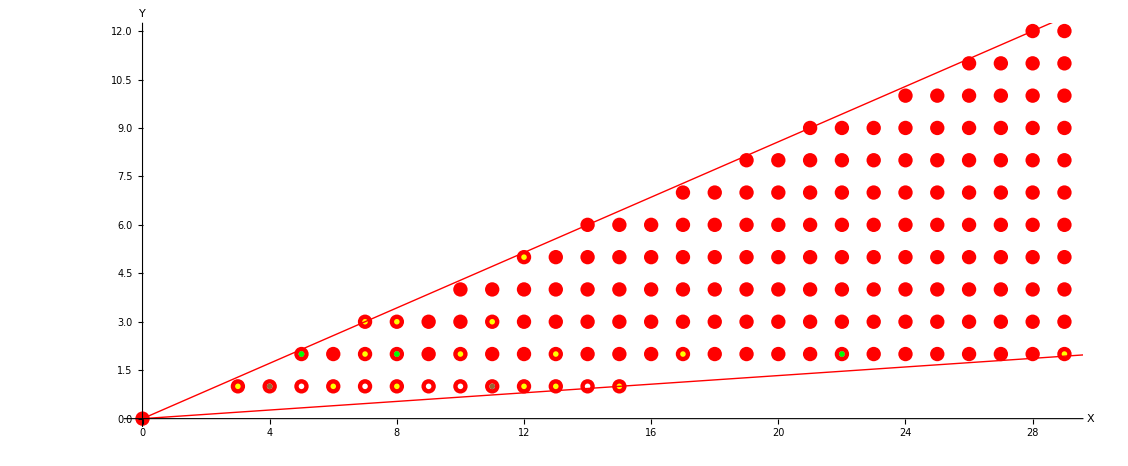

Huecos -> 10

Ps -> 5

Sg -> 3

Out getsinfo -> {{1,3,5,8,10},{3,5,10},3}

N.ba de #C 3

N.ba de #C 1

N.ba de #C 2

{0.015625,{{{{3,1},{5,2},{6,1},{7,2},{7,3},{8,1},{8,2},{8,3},{10,2},{11,3},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{29,2}},{{4,1},{5,1},{7,1},{9,1},{10,1},{11,1},{14,1},{22,2}},0},{{{3,1},{5,2},{6,1},{7,2},{7,3},{8,1},{8,3},{10,2},{11,3},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{22,2},{29,2}},{{4,1},{5,1},{7,1},{8,2},{9,1},{10,1},{11,1},{14,1}},0},{{{3,1},{4,1},{5,2},{6,1},{7,2},{7,3},{8,1},{8,2},{8,3},{10,2},{11,3},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{22,2},{29,2}},{{5,1},{7,1},{9,1},{10,1},{11,1},{14,1}},1},{{{3,1},{4,1},{6,1},{7,2},{7,3},{8,1},{8,2},{8,3},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{22,2},{29,2}},{{5,1},{5,2},{7,1},{9,1},{10,1},{14,1}},1},{{{3,1},{5,2},{6,1},{7,2},{7,3},{8,1},{8,2},{8,3},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{22,2},{29,2}},{{4,1},{5,1},{7,1},{9,1},{10,1},{14,1}},1}}}

5

Out getsinfo -> {{1,3,5,8,10},{3,5,10},3}

N.ba de #C 3

N.ba de #C 1

N.ba de #C 2

N.ba irreducibles 1 -> 5

N.ba irreducibles 2 -> 3

Alg 1 -----

{{{{3,1},{5,2},{6,1},{7,2},{7,3},{8,1},{8,2},{8,3},{10,2},{11,3},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{29,2}},{{4,1},{5,1},{7,1},{9,1},{10,1},{11,1},{14,1},{22,2}}},{{{3,1},{5,2},{6,1},{7,2},{7,3},{8,1},{8,3},{10,2},{11,3},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{22,2},{29,2}},{{4,1},{5,1},{7,1},{8,2},{9,1},{10,1},{11,1},{14,1}}},{{{3,1},{4,1},{5,2},{6,1},{7,2},{7,3},{8,1},{8,2},{8,3},{10,2},{11,3},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{22,2},{29,2}},{{5,1},{7,1},{9,1},{10,1},{11,1},{14,1}}},{{{3,1},{4,1},{6,1},{7,2},{7,3},{8,1},{8,2},{8,3},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{22,2},{29,2}},{{5,1},{5,2},{7,1},{9,1},{10,1},{14,1}}},{{{3,1},{5,2},{6,1},{7,2},{7,3},{8,1},{8,2},{8,3},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{22,2},{29,2}},{{4,1},{5,1},{7,1},{9,1},{10,1},{14,1}}}}

Alg 2 -----

{0.015625,{{{{{3,1},{5,2},{6,1},{7,2},{7,3},{8,1},{8,2},{10,2},{12,1},{13,1},{13,2},{15,1},{17,2},{29,2}},{{4,1},{5,1},{7,1},{9,1},{10,1},{11,1},{14,1},{22,2}}},0},{{{{3,1},{5,2},{6,1},{7,2},{7,3},{8,1},{10,2},{12,1},{13,1},{13,2},{15,1},{17,2},{22,2},{29,2}},{{4,1},{5,1},{7,1},{8,2},{9,1},{10,1},{11,1},{14,1}}},0},{{{{3,1},{4,1},{6,1},{7,3},{8,1},{8,3},{11,1},{12,1},{12,5},{13,1},{13,2},{15,1},{29,2}},{{5,1},{5,2},{7,1},{9,1},{10,1},{14,1}}},1}}}

Algoritmo 1 -> 3

Algoritmo 2 -> 5

```mathematica
(*PRUEBA CON PSEUDOSIMETRICOS Y QUE DEPURA*)
irreduciblesExample={{{{3,1},{6,1},{7,2},{7,3},{8,1},{8,3},{10,2},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{29,2},{11,3}},{{4,1},{5,1},{5,2},{7,1},{8,2},{9,1},{10,1},{11,1},{14,1},{22,2}}},{{-1,15},{3,-7}}}

(*Representación gráfica*)
Plot2DSemigAll[irreduciblesExample[[1,1]],irreduciblesExample[[1,2]]];

(*Propiedades semigrupo*)
Print["Huecos -> ",Length[irreduciblesExample[[1,2]]]]
p = GetPseudoFrobenius[irreduciblesExample[[1,1]],irreduciblesExample[[1,2]]];
Print["Ps -> ",Length[ GetPseudoFrobenius[irreduciblesExample[[1,1]],irreduciblesExample[[1,2]]]]];
Print["Sg -> ",Length[ GetEspGaps[p,irreduciblesExample[[1,2]]]]]

(*Algoritmo 1*)
Timing [testirr = GetIrreducibles[irreduciblesExample[[1,1]],irreduciblesExample[[1,2]],irreduciblesExample[[2]],False]]
Length[testirr]

(*Algoritmo 2*)
Timing [testminirr = GetMinimalsIrreducibles[irreduciblesExample[[1,1]],irreduciblesExample[[1,2]],irreduciblesExample[[2]],False,False]]

(*N.ba de irreducibles*)
Print["Algoritmo 1 -> ",Length[testminirr]]
Print["Algoritmo 2 -> ",Length[testirr]]
```

### Ejemplo Simetricos&Pseudosim

Estos dos ejemplos son obtenidos a partir del algoritmo 2 aplicado sobre el siguiente semigrupo. Tomaremos los úl:

{{{{3,1},{4,1},{6,1},{7,3},{8,1},{8,3},{11,1},{12,1},{12,5},{13,1},{13,2},{15,1},{29,2}},{{5,1},{5,2},{7,1},{9,1},{10,1},{14,1}}},1}

Vectores de los rayos extremales= {{15.,1.},{7.,3.}}

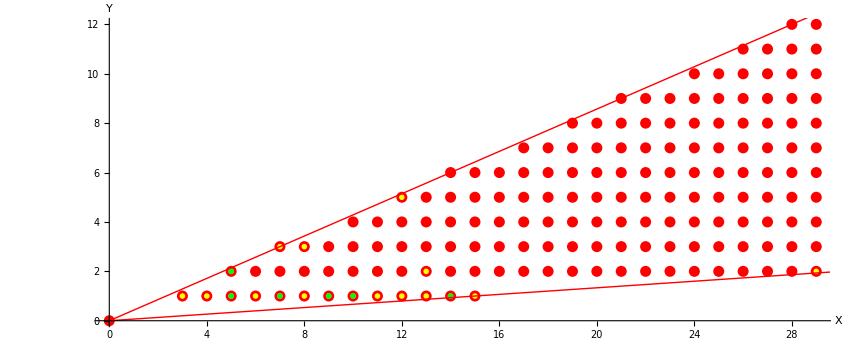

Huecos -> 6

Ps -> 6

Sg -> 6

```mathematica
(*Simetrico*)
simsExample={{{{3,1},{4,1},{6,1},{7,3},{8,1},{8,3},{11,1},{12,1},{12,5},{13,1},{13,2},{15,1},{29,2}},{{5,1},{5,2},{7,1},{9,1},{10,1},{14,1}}},1}

(*Representación gráfica*)
Plot2DSemigAll[simsExample[[1,1]],simsExample[[1,2]]];

(*Propiedades semigrupo*)
Print["Huecos -> ",Length[simsExample[[1,2]]]]
p = GetPseudoFrobenius[simsExample[[1,1]],simsExample[[1,2]]];
Print["Ps -> ",Length[ p ]];
Print["Sg -> ",Length[ GetEspGaps[p,simsExample[[1,2]]]]]
```

{{{{3,1},{5,2},{6,1},{7,2},{7,3},{8,1},{10,2},{12,1},{13,1},{13,2},{15,1},{17,2},{22,2},{29,2}},{{4,1},{5,1},{7,1},{8,2},{9,1},{10,1},{11,1},{14,1}}},0}

Vectores de los rayos extremales= {{15.,1.},{7.,3.}}

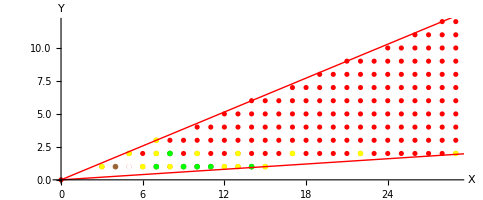

Huecos -> 8

Ps -> 7

Sg -> 6

{{{{3,1},{5,2},{6,1},{7,2},{7,3},{8,1},{10,2},{12,1},{13,1},{13,2},{15,1},{17,2},{22,2},{29,2}},{{4,1},{5,1},{7,1},{8,2},{9,1},{10,1},{11,1},{14,1}}},0}

```mathematica
(*Pseudosimétrico*)
pseusimsExample={{{{3,1},{5,2},{6,1},{7,2},{7,3},{8,1},{10,2},{12,1},{13,1},{13,2},{15,1},{17,2},{22,2},{29,2}},{{4,1},{5,1},{7,1},{8,2},{9,1},{10,1},{11,1},{14,1}}},0}

(*Representación gráfica*)
Plot2DSemigAll[pseusimsExample[[1,1]],pseusimsExample[[1,2]]];

(*Propiedades semigrupo*)
Print["Huecos -> ",Length[pseusimsExample[[1,2]]]]
p = GetPseudoFrobenius[pseusimsExample[[1,1]],pseusimsExample[[1,2]]];
Print["Ps -> ",Length[ p ]];
Print["Sg -> ",Length[ GetEspGaps[p,pseusimsExample[[1,2]]]]]

pseusimsExample={{{{3,1},{5,2},{6,1},{7,2},{7,3},{8,1},{10,2},{12,1},{13,1},{13,2},{15,1},{17,2},{22,2},{29,2}},{{4,1},{5,1},{7,1},{8,2},{9,1},{10,1},{11,1},{14,1}}},0}
```

## Ejemplos Buenos

### Ejemplo 1 Algoritmo 1 y 2

```mathematica
(*PRUEBA CON PSEUDOSIMETRICOS Y QUE DEPURA*)
pruebaConPseudos={{{{3,1},{6,1},{7,2},{7,3},{8,1},{8,3},{10,2},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{29,2},{11,3}},{{4,1},{5,1},{5,2},{7,1},{8,2},{9,1},{10,1},{11,1},{14,1},{22,2}}},{{-1,15},{3,-7}}}

Plot2DSemigAll[pruebaConPseudos[[1,1]],pruebaConPseudos[[1,2]]];

Print["Huecos -> ",Length[pruebaConPseudos[[1,2]]]]
p = GetPseudoFrobenius[pruebaConPseudos[[1,1]],pruebaConPseudos[[1,2]]];
Print["Ps -> ",Length[ GetPseudoFrobenius[pruebaConPseudos[[1,1]],pruebaConPseudos[[1,2]]]]];
Print["Sg -> ",Length[ GetEspGaps[p,pruebaConPseudos[[1,2]]]]]

Timing [testirr = GetIrreducibles[pruebaConPseudos[[1,1]],pruebaConPseudos[[1,2]],pruebaConPseudos[[2]],False]];
Length[testirr]

Timing [testminirr = GetMinimalsIrreducibles[pruebaConPseudos[[1,1]],pruebaConPseudos[[1,2]],pruebaConPseudos[[2]],False,False]]
Length[testminirr]
Length[testirr]
```

{{{{3,1},{6,1},{7,2},{7,3},{8,1},{8,3},{10,2},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{29,2},{11,3}},{{4,1},{5,1},{5,2},{7,1},{8,2},{9,1},{10,1},{11,1},{14,1},{22,2}}},{{-1,15},{3,-7}}}

Huecos -> 10

Ps -> 5

Sg -> 3

Out getsinfo -> {{1,3,5,8,10},{3,5,10},3}

N.ba de #C 3

N.ba de #C 8

N.ba de #C 23

N.ba de #C 47

N.ba de #C 71

N.ba de #C 76

N.ba de #C 56

N.ba de #C 28

10

Out getsinfo -> {{1,3,5,8,10},{3,5,10},3}

N.ba de #C 3

N.ba de #C 8

N.ba de #C 23

N.ba de #C 47

N.ba de #C 71

N.ba de #C 76

N.ba de #C 56

N.ba de #C 28

N.ba irreducibles 1 -> 10

N.ba irreducibles 2 -> 3

Alg 1 -----

{{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,2},{7,3},{8,1},{8,2},{8,3},{10,2},{11,3},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{29,2}},{{7,1},{9,1},{10,1},{11,1},{14,1},{22,2}}},{{{3,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{8,3},{9,1},{10,1},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{14,1},{15,1},{17,2},{22,2},{29,2}},{{4,1},{5,1},{8,2}}},{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{8,2},{8,3},{9,1},{10,1},{10,2},{11,3},{12,1},{12,5},{13,1},{13,2},{14,1},{15,1},{17,2},{22,2},{29,2}},{{11,1}}},{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{8,2},{8,3},{9,1},{10,1},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{15,1},{17,2},{22,2},{29,2}},{{14,1}}},{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{8,2},{8,3},{9,1},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{14,1},{15,1},{17,2},{22,2},{29,2}},{{10,1}}},{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{8,2},{8,3},{10,1},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{14,1},{15,1},{17,2},{22,2},{29,2}},{{9,1}}},{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,2},{7,3},{8,1},{8,2},{8,3},{9,1},{10,1},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{14,1},{15,1},{17,2},{22,2},{29,2}},{{7,1}}},{{{3,1},{4,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{8,2},{8,3},{9,1},{10,1},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{14,1},{15,1},{17,2},{22,2},{29,2}},{{5,1}}},{{{3,1},{5,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{8,2},{8,3},{9,1},{10,1},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{14,1},{15,1},{17,2},{22,2},{29,2}},{{4,1}}},{{{3,1},{4,1},{5,1},{6,1},{7,1},{7,2},{7,3},{8,1},{8,2},{8,3},{9,1},{10,1},{10,2},{11,1},{11,3},{12,1},{12,5},{13,1},{13,2},{14,1},{15,1},{17,2},{22,2},{29,2}},{{5,2}}}}

Alg 2 -----

{0.96875,{{{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{12,1},{13,1},{15,1},{29,2}},{{7,1},{9,1},{10,1},{11,1},{14,1},{22,2}}},0},{{{{3,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{13,1},{14,1},{15,1}},{{4,1},{5,1},{8,2}}},0},{{{{3,1},{4,1},{5,1},{6,1},{7,1},{7,3},{8,1},{8,3},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{15,1}},{{5,2}}},1}}}

3

10

### Ejemplo Simetricos&Pseudosim

Estos dos ejemplos son obtenidos a partir del algoritmo 2 aplicado sobre el siguiente semigrupo. Tomaremos los úl:

{{{{3,1},{4,1},{5,1},{6,1},{7,1},{7,3},{8,1},{8,3},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{15,1}},{{5,2}}},1}

Vectores de los rayos extremales= {{15.,1.},{7.,3.}}

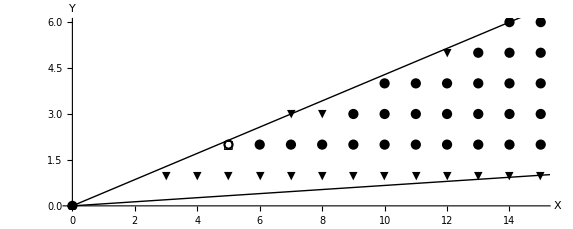

Huecos -> 1

Ps -> 1

Sg -> 1

```mathematica
(*Simetrico*)
simsExample={{{{3,1},{4,1},{5,1},{6,1},{7,1},{7,3},{8,1},{8,3},{9,1},{10,1},{11,1},{12,1},{12,5},{13,1},{14,1},{15,1}},{{5,2}}},1}

(*Representación gráfica*)
Plot2DSemigAllBW[simsExample[[1,1]],simsExample[[1,2]]];

(*Propiedades semigrupo*)
Print["Huecos -> ",Length[simsExample[[1,2]]]]
p = GetPseudoFrobenius[simsExample[[1,1]],simsExample[[1,2]]];
Print["Ps -> ",Length[ GetPseudoFrobenius[simsExample[[1,1]],simsExample[[1,2]]]]];
Print["Sg -> ",Length[ GetEspGaps[p,simsExample[[1,2]]]]]
```

{{{{3,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{13,1},{14,1},{15,1}},{{4,1},{5,1},{8,2}}},0}

Vectores de los rayos extremales= {{15.,1.},{7.,3.}}

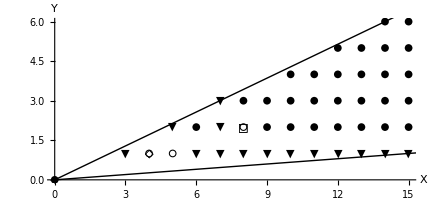

Huecos -> 3

Ps -> 2

Sg -> 1

```mathematica
(*Pseudosimétrico 1*)
pseusimsExample={{{{3,1},{5,2},{6,1},{7,1},{7,2},{7,3},{8,1},{9,1},{10,1},{11,1},{12,1},{13,1},{14,1},{15,1}},{{4,1},{5,1},{8,2}}},0}

(*Representación gráfica*)
Plot2DSemigAllBW[pseusimsExample[[1,1]],pseusimsExample[[1,2]]];

(*Propiedades semigrupo*)
Print["Huecos -> ",Length[pseusimsExample[[1,2]]]]
p = GetPseudoFrobenius[pseusimsExample[[1,1]],pseusimsExample[[1,2]]];
Print["Ps -> ",Length[ GetPseudoFrobenius[pseusimsExample[[1,1]],pseusimsExample[[1,2]]]]];
Print["Sg -> ",Length[ GetEspGaps[p,pseusimsExample[[1,2]]]]]
```

{{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{12,1},{13,1},{15,1},{29,2}},{{7,1},{9,1},{10,1},{11,1},{14,1},{22,2}}},0}

Vectores de los rayos extremales= {{15.,1.},{7.,3.}}

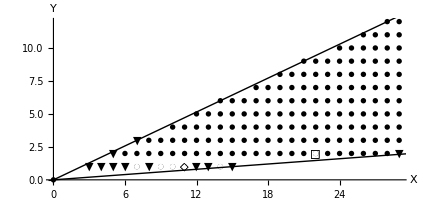

Huecos -> 6

Ps -> 2

Sg -> 1

```mathematica
(*Pseudosimétrico 2*)
pseusimsExample={{{{3,1},{4,1},{5,1},{5,2},{6,1},{7,3},{8,1},{12,1},{13,1},{15,1},{29,2}},{{7,1},{9,1},{10,1},{11,1},{14,1},{22,2}}},0}

(*Representación gráfica*)
Plot2DSemigAllBW[pseusimsExample[[1,1]],pseusimsExample[[1,2]]];

(*Propiedades semigrupo*)
Print["Huecos -> ",Length[pseusimsExample[[1,2]]]]
p = GetPseudoFrobenius[pseusimsExample[[1,1]],pseusimsExample[[1,2]]];
Print["Ps -> ",Length[ GetPseudoFrobenius[pseusimsExample[[1,1]],pseusimsExample[[1,2]]]]];
Print["Sg -> ",Length[ GetEspGaps[p,pseusimsExample[[1,2]]]]]
```

## Prob para alg 3

```mathematica
GCD[{2,3,4,5}]
```

{2,3,4,5}

```mathematica
Apply[GCD,{2,4,6,2}]==1
```

False

```mathematica
Divisors[Apply[GCD,{2,4,2,2}]]
```

{1,2}

```mathematica
MemberQ[{1,1},{{1,2},{1,3}}]
MemberQ[#
```

False

```mathematica
Table[If[i==0,Return[None]],{i,{1,2,3,4}}]
```

{Null,Null,Null,Null}

```mathematica
Prueba[A_,Eq_,verb_]:= Module[{a,x,i,gcd},
	If[A=={},
		Return[False]
	];

	Do[
		x=A[1];
		If[¬InCone[A[1],Eq], Return[False]];
		
		gcd=Divisors[Apply[GCD,A[1]]];
		
		If[ gcd ≠ 1,
			Table[If[¬MemberQ[x/i,A],Return[False]],{i,gcd}]
		]

	,{x,A}]
]
```

```mathematica
Prueba[{3,21},True,True]
```

False

```mathematica
If[a=2 ==2,4]
```

4

```mathematica
Do[Print[i],{i,{32,32}}]
```

32

32